```mathematica
QUANTIF =20000;
```

```mathematica
Quantification[val_] := If[val<0,0,If[val>QUANTIF,QUANTIF,Round[val]]]
```

```mathematica
sx = 30;
sy = 30;
```

```mathematica
epsilon = 10^(-10)//N;
fValuation[x_,y_] := Quantification[QUANTIF*0.5*((((x - sx/2.0)^2)/((sx/2.0)^2))+(((y - sy/2.0)^2)/((sy/2.0)^2)))];
fValuation[x_,y_] := Quantification[QUANTIF*(0.5*(1 + Cos[2 * Pi * x / (sx/3.0)]))*(0.5*(1 + Cos[2 * Pi * y / (sy/1.0)]))];
fValuation[x_,y_] := Quantification[QUANTIF*(1.0 - 0.5*(1 + Cos[2 * Pi * Sqrt[((x -sx/2)/ (sx/3.0))^2+((y-sy/2) / (sy/3.0))^2]]))]; 
fValuation[x_,y_] := Quantification[QUANTIF*(1.0 - 0.5*(1 + Cos[2 * Pi * Sqrt[((x -sx/2)/ (sx/5.0))^2+((y-sy/2) / (sy/5.0))^2]]))];
```

# Morse & Morpho

# Fonction Continue Initiale

```mathematica
Print[Image[Table[fValuation[x,y],{x,1,sx,0.1},{y,1,sy,0.1}],ImageSize->300]//ImageAdjust]
```

-Graphics-

# Définitions

```mathematica
(* contre effets de bords de fonction opposée duale *)
RemettreBordàZéro[ValuedVertices_,ValuedEdges_,ValuedFaces_]:=Block[{FinalValuedVertices,FinalValuedEdges,FinalValuedFaces,NbFaces,NbEdges,NbVertices,numeroface,numeroedge,numerovertex},

NbFaces = Dimensions[ValuedFaces][[1]];
NbEdges = Dimensions[ValuedEdges][[1]];
NbVertices = Dimensions[ValuedVertices][[1]];

FinalValuedFaces = ValuedFaces;
FinalValuedEdges = ValuedEdges;
FinalValuedVertices = ValuedVertices;

(* MISE A ZERO DES FACES DU BORD *)
For[numeroface = 1, numeroface ≤ NbFaces,numeroface++,{
If[ValuedFaces[[numeroface]][[4]] == "bord",
FinalValuedFaces[[numeroface]][[2]] = 0;
];
}];

(* MISE A ZERO DES EDGES DU BORD *)
For[numeroedge = NbFaces + 1, numeroedge ≤ NbFaces+NbEdges,numeroedge++,{
If[ValuedEdges[[numeroedge-NbFaces]][[4]] == "bord",
FinalValuedEdges[[numeroedge - NbFaces]][[2]] = 0;
];
}];

(* MISE A ZERO DES VERTICES DU BORD *)
For[numerovertex = NbFaces + NbEdges+1, numerovertex ≤ NbFaces+NbEdges+NbVertices,numerovertex++,{
If[ValuedVertices[[numerovertex - NbFaces - NbEdges]][[4]] == "bord",
FinalValuedVertices[[numerovertex - NbFaces - NbEdges]][[2]] = 0;
];
}];

{FinalValuedVertices,FinalValuedEdges,FinalValuedFaces}
];
```

```mathematica
RechercheVertexBord[ValuedVertices_,ValuedEdges_,ValuedFaces_]:=Block[{xminimal,numerovertexbord,numerovertex,NbFaces,NbEdges,NbVertices},
(* on prend n'importe quel vertex qui minimise x *)
NbFaces = Dimensions[ValuedFaces][[1]];
NbEdges = Dimensions[ValuedEdges][[1]];
NbVertices = Dimensions[ValuedVertices][[1]];

xminimal = ∞;
numerovertexbord = -1;

For[numerovertex = NbFaces+NbEdges+1, numerovertex ≤ NbFaces+NbEdges+NbVertices,numerovertex++,{
If[ValuedVertices[[numerovertex-NbFaces-NbEdges]][[1]][[1]][[1]] < xminimal,{
xminimal = ValuedVertices[[numerovertex-NbFaces-NbEdges]][[1]][[1]][[1]];
numerovertexbord = numerovertex;
};]
}];
numerovertexbord
];
```

```mathematica
(* Coordonnées des vertices *)
Maillage[cptx_,cpty_]:={cptx + If[Mod[cpty,2]==1,0.5,0],cpty}
```

```mathematica
(* Coordonnées des edges finissant en ce point *)
Edges[cptx_,cpty_,sx_,sy_]:= Block[{liste},
liste = {};
If[cptx ≥ 1,
liste = Append[liste,{Maillage[cptx-1,cpty],Maillage[cptx,cpty]}];
];
If[cptx ≥ 1&& cpty ≥ 1 && Mod[cpty,2] == 0,
liste = Append[liste,{Maillage[cptx-1,cpty-1],Maillage[cptx,cpty]}];
];
If[cpty ≥ 1 && Mod[cpty,2] == 1,
liste = Append[liste,{Maillage[cptx,cpty-1],Maillage[cptx,cpty]}];
];
If[cptx ≥ 1 && cpty +1 ≤ sy  && Mod[cpty,2] == 0,
liste = Append[liste,{Maillage[cptx-1,cpty+1],Maillage[cptx,cpty]}];
];
If[cptx ≥ 0 && cpty +1 ≤ sy  && Mod[cpty,2] == 1,
liste = Append[liste,{Maillage[cptx,cpty+1],Maillage[cptx,cpty]}];
];
liste
];
```

```mathematica
(* Coordonnées des edges finissant en ce point *)
FaceUp[cptx_,cpty_]:= If[Mod[cpty,2]==1,{Maillage[cptx-1,cpty-1],Maillage[cptx,cpty-1],Maillage[cptx-1,cpty]},{Maillage[cptx-1,cpty-1],Maillage[cptx,cpty-1],Maillage[cptx,cpty]}];
FaceDown[cptx_,cpty_]:= If[Mod[cpty,2]==1,{Maillage[cptx-1,cpty],Maillage[cptx-1,cpty+1],Maillage[cptx,cpty+1]},{Maillage[cptx-1,cpty+1],Maillage[cptx,cpty+1],Maillage[cptx,cpty]}];
```

```mathematica
ComputePseudoManifold[sx_,sy_]:=Block[{vertices,edges,facesUP,facesDOWN,listeverticesplot,listeedgesplot,listefacesUPplot,listefacesDOWNplot,faces},
vertices = Flatten[Table[Maillage[x,y],{x,0,sx},{y,0,sy}],1];
listeverticesplot = Table[Disk[vertices[[cpt]],0.1],{cpt,1,Dimensions[vertices][[1]]}];
edges =  Flatten[Table[Edges[x,y,sx,sy],{x,0,sx},{y,0,sy}],1];
listeedgesplot = Table[Line[edges[[cpt]]],{cpt,1,Dimensions[edges][[1]]}];
facesUP = Flatten[Table[FaceUp[x,y],{x,1,sx},{y,1,sy}],1];
listefacesUPplot = Table[Polygon[facesUP[[cpt]]],{cpt,1,Dimensions[facesUP][[1]]}];
facesDOWN = Flatten[Table[FaceDown[x,y],{x,1,sx},{y,0,sy-1}],1];
faces = facesUP~Union~facesDOWN;
listefacesDOWNplot = Table[Polygon[facesDOWN[[cpt]]],{cpt,1,Dimensions[facesDOWN][[1]]}];
Print[Graphics[{Red,listefacesUPplot,Pink,listefacesDOWNplot, Black,Thickness[0.002],listeedgesplot,Blue,listeverticesplot}]];
{vertices,edges,faces}
];
```

```mathematica
VerticesFromEdge[edge_] := {edge[[1]],edge[[2]]}
```

```mathematica
ComputeParentsDirects[ParentsDirectsParNumero_,Numero_] := Block[{listeenfants,listeRelationsDeParente,result},
listeenfants = Table[ParentsDirectsParNumero[[cpt]][[1]],{cpt,1,Dimensions[ParentsDirectsParNumero][[1]]}];
If[MemberQ[listeenfants,Numero],{
listeRelationsDeParente = Position[listeenfants,Numero];
result = Table[ParentsDirectsParNumero[[listeRelationsDeParente[[cpt]][[1]]]][[2]],{cpt,1,Dimensions[listeRelationsDeParente][[1]]}];
},{
result = -1;
}];
result
];
```

```mathematica
ComputeEnfantsDirects[EnfantsDirectsParNumero_,Numero_] := Block[{listeparents,listeRelationsDEnfants,result},
listeparents = Table[EnfantsDirectsParNumero[[cpt]][[1]],{cpt,1,Dimensions[EnfantsDirectsParNumero][[1]]}];
If[MemberQ[listeparents,Numero],{
listeRelationsDEnfants = Position[listeparents,Numero];
result = Table[EnfantsDirectsParNumero[[listeRelationsDEnfants[[cpt]][[1]]]][[2]],{cpt,1,Dimensions[listeRelationsDEnfants][[1]]}];
},{
result = -1;
}];
result
];
```

```mathematica
EdgesFromFace[face_]:={{face[[1]],face[[2]]},{face[[2]],face[[3]]},{face[[3]],face[[1]]}}
```

```mathematica
PLOTNICO[ValuedFaces_,ValuedEdges_,ValuedVertices_]:=Block[{listefacesplot,listeedgesplot,listeverticesplot,listcolorsfaces,grayface,grayedge,grayvertex,grayface0,grayedge0,grayvertex0,listcolorsedges,listcolorsvertices,MAX},

grayface0[cpt_]:=ValuedFaces[[cpt]][[2]];
grayedge0[cpt_]:=ValuedEdges[[cpt]][[2]];
grayvertex0[cpt_]:=ValuedVertices[[cpt]][[2]];

(* calcul du max pour renormalisation pour l'affichage *)
MAX = Max[{
Table[grayface0[cpt],{cpt,1,Dimensions[ValuedFaces][[1]]}],
Table[grayedge0[cpt],{cpt,1,Dimensions[ValuedEdges][[1]]}],
Table[grayvertex0[cpt],{cpt,1,Dimensions[ValuedVertices][[1]]}]
}];
If[MAX > 0,{
(* renormalisés *)
grayface[cpt_]:=ValuedFaces[[cpt]][[2]]/MAX//N;
grayedge[cpt_]:=ValuedEdges[[cpt]][[2]]/MAX//N;
grayvertex[cpt_]:=ValuedVertices[[cpt]][[2]]/MAX//N;

(* precompute *)
listcolorsfaces = Table[RGBColor[{grayface[cpt],grayface[cpt],grayface[cpt]}],{cpt,1,Dimensions[ValuedFaces][[1]]}];
listcolorsedges = Table[RGBColor[{grayedge[cpt],grayedge[cpt],grayedge[cpt]}],{cpt,1,Dimensions[ValuedEdges][[1]]}];
listcolorsvertices = Table[RGBColor[{grayvertex[cpt],grayvertex[cpt],grayvertex[cpt]}],{cpt,1,Dimensions[ValuedVertices][[1]]}];
},{

(* precompute *)
listcolorsfaces = Table[Blue,{cpt,1,Dimensions[ValuedFaces][[1]]}];
listcolorsedges = Table[Green,{cpt,1,Dimensions[ValuedEdges][[1]]}];
listcolorsvertices = Table[Red,{cpt,1,Dimensions[ValuedVertices][[1]]}];

}];

listefacesplot = Table[{listcolorsfaces[[cpt]],Polygon[ValuedFaces[[cpt]][[1]]]},{cpt,1,Dimensions[ValuedFaces][[1]]}];
listeedgesplot = Table[{listcolorsedges[[cpt]],Line[ValuedEdges[[cpt]][[1]]]},{cpt,1,Dimensions[ValuedEdges][[1]]}];
listeverticesplot = Table[{listcolorsvertices[[cpt]],Disk[ValuedVertices[[cpt]][[1]][[1]],0.1]},{cpt,1,Dimensions[ValuedVertices][[1]]}];

{listefacesplot,listeedgesplot,listeverticesplot,Graphics[{listefacesplot, Black,Thickness[0.004],listeedgesplot,Blue,listeverticesplot}]}
];
```

```mathematica
PLOTNICOCOMPLEXEPRIMAL[ValuedFaces_,ValuedEdges_,ValuedVertices_]:=Block[{listefacesplot,listeedgesplot,listeverticesplot,listcolorsfaces,grayface,grayedge,grayvertex,grayface0,grayedge0,grayvertex0,listcolorsedges,listcolorsvertices,MAX},

grayface0[cpt_]:=ValuedFaces[[cpt]][[2]];
grayedge0[cpt_]:=ValuedEdges[[cpt]][[2]];
grayvertex0[cpt_]:=ValuedVertices[[cpt]][[2]];

(* calcul du max pour renormalisation pour l'affichage *)
MAX = Max[{
Table[grayface0[cpt],{cpt,1,Dimensions[ValuedFaces][[1]]}],
Table[grayedge0[cpt],{cpt,1,Dimensions[ValuedEdges][[1]]}],
Table[grayvertex0[cpt],{cpt,1,Dimensions[ValuedVertices][[1]]}]
}];

If[MAX >0,{
(* renormalisés *)
grayface[cpt_]:=ValuedFaces[[cpt]][[2]]/MAX//N;
grayedge[cpt_]:=ValuedEdges[[cpt]][[2]]/MAX//N;
grayvertex[cpt_]:=ValuedVertices[[cpt]][[2]]/MAX//N;

(* precompute *)
listcolorsfaces = Table[RGBColor[{grayface[cpt],grayface[cpt],grayface[cpt]}],{cpt,1,Dimensions[ValuedFaces][[1]]}];
listcolorsedges = Table[RGBColor[{grayedge[cpt],grayedge[cpt],grayedge[cpt]}],{cpt,1,Dimensions[ValuedEdges][[1]]}];
listcolorsvertices = Table[RGBColor[{grayvertex[cpt],grayvertex[cpt],grayvertex[cpt]}],{cpt,1,Dimensions[ValuedVertices][[1]]}];

},{

(* precompute *)
listcolorsfaces = Table[Blue,{cpt,1,Dimensions[ValuedFaces][[1]]}];
listcolorsedges = Table[Green,{cpt,1,Dimensions[ValuedEdges][[1]]}];
listcolorsvertices = Table[Red,{cpt,1,Dimensions[ValuedVertices][[1]]}];

}];

listefacesplot = Table[{listcolorsfaces[[cpt]],Polygon[ValuedFaces[[cpt]][[1]]]},{cpt,1,Dimensions[ValuedFaces][[1]]}];
listeedgesplot = Table[{Thickness[0.04],listcolorsedges[[cpt]],Line[ValuedEdges[[cpt]][[1]]]},{cpt,1,Dimensions[ValuedEdges][[1]]}];
listeverticesplot = Table[{listcolorsvertices[[cpt]],Disk[ValuedVertices[[cpt]][[1]][[1]],0.45]},{cpt,1,Dimensions[ValuedVertices][[1]]}];
{listefacesplot,listeedgesplot,listeverticesplot,Graphics[{listefacesplot,listeedgesplot,listeverticesplot}]}
];
```

```mathematica
(*On crée une structure qui donne un complexe simplicial (valué) avec ses relations de parenté par face -- ON VERRA PLUS TARD LA REVALUATION !!! *)
ComputeValuedPseudoManifold[sx_,sy_]:=Block[{facesUP,facesDOWN,listeverticesplot,listeedgesplot,listefacesplot,faces,ValuesOfFaces,ValuedFaces,NbFaces,numeroedgecourant,numeroface,listeedges,numeroedge,NbEdges,numeroedgeETUDIE,edgesSEULS,ValuedEdges,newedge,numerofaceparente,ParentsDirectsParNumero,EnfantsDirectsParNumero,numerovertexcourant,vertexSEULS,ValuedVertices,numeroRELATIFedge,listevertices,numeroedgeparent,numerovertex,newvertex,numerovertexETUDIE,NbVertices,NumerosParentsEdge,xbar,ybar,tousparentsdansbord,NumerosParentsVertex,GRAPHIQUE},
facesUP = Flatten[Table[{FaceUp[x,y],If[x≤ 2 ||x ≥ sx - 1 || y ≤ 2 || y≥ sy- 1,{0,"bord"},{1,"Intérieur"}]},{x,1,sx},{y,1,sy}],1];
facesDOWN = Flatten[Table[{FaceDown[x,y],If[x≤ 2 ||x ≥ sx -1 || y ≤ 1 || y≥ sy-2,{0,"bord"},{1,"Intérieur"}]},{x,1,sx},{y,0,sy-1}],1];
faces = facesUP~Join~facesDOWN;
ValuedFaces =Table[{faces[[cpt]][[1]],faces[[cpt]][[2]][[1]],cpt,faces[[cpt]][[2]][[2]]},{cpt,1,Dimensions[faces][[1]]}];

NbFaces =  Dimensions[faces][[1]];
Print["NbFaces = ",NbFaces];

numeroedgecourant =NbFaces+1;
edgesSEULS = {};
ValuedEdges = {};
ParentsDirectsParNumero = {};
EnfantsDirectsParNumero = {};
For[numeroface = 1, numeroface ≤  NbFaces, numeroface++,{
listeedges = EdgesFromFace[ValuedFaces[[numeroface]][[1]]];
numerofaceparente = ValuedFaces[[numeroface]][[3]];
For[numeroedge = 1, numeroedge ≤ 3, numeroedge++,{
newedge = listeedges[[numeroedge]];
(* si jamais nouveau, on attribue un nouveau numéro *)
If[MemberQ[edgesSEULS,newedge]== False,{
numeroedgeETUDIE = numeroedgecourant;
edgesSEULS = Append[edgesSEULS,newedge];
ValuedEdges = Append[ValuedEdges,{newedge,1.0,numeroedgeETUDIE}];
numeroedgecourant ++;
},{
numeroedgeETUDIE = NbFaces + Position[edgesSEULS,newedge][[1,1]];
}];
(* on rajoute ses relations de parente qui sont nouvelles car face regardée pour la premiere fois *)
ParentsDirectsParNumero = Append[ParentsDirectsParNumero,numeroedgeETUDIE -> numerofaceparente];
EnfantsDirectsParNumero = Append[EnfantsDirectsParNumero,numerofaceparente -> numeroedgeETUDIE];
}];
}];
NbEdges = Dimensions[edgesSEULS][[1]];
Print["NbEdges = ",NbEdges];


numerovertexcourant =NbFaces+NbEdges + 1;
vertexSEULS = {};
ValuedVertices = {};
For[numeroRELATIFedge = 1, numeroRELATIFedge ≤ NbEdges, numeroRELATIFedge++,{
listevertices = VerticesFromEdge[ValuedEdges[[numeroRELATIFedge]][[1]]];
numeroedgeparent = ValuedEdges[[numeroRELATIFedge]][[3]];
For[numerovertex = 1, numerovertex ≤ 2,numerovertex++,{
newvertex = listevertices[[numerovertex]];
(* si jamais nouveau, on attribue un nouveau numéro *)
If[MemberQ[vertexSEULS,newvertex]== False,{
numerovertexETUDIE = numerovertexcourant;
vertexSEULS = Append[vertexSEULS,newvertex];
ValuedVertices = Append[ValuedVertices,{{newvertex},RandomReal[],numerovertexETUDIE}];
numerovertexcourant ++;
},{
numerovertexETUDIE = NbFaces + NbEdges + Position[vertexSEULS,newvertex][[1,1]];
}];
(* on rajoute ses relations de parente qui sont nouvelles car face regardée pour la premiere fois *)
ParentsDirectsParNumero = Append[ParentsDirectsParNumero,numerovertexETUDIE -> numeroedgeparent];
EnfantsDirectsParNumero = Append[EnfantsDirectsParNumero,numeroedgeparent -> numerovertexETUDIE];
}];
}];
NbVertices = Dimensions[vertexSEULS][[1]];
Print["NbVertices = ",NbVertices];

(* VALUATION DES FACES *)
For[numeroface = 1,numeroface ≤ NbFaces,numeroface++,{
{xbar,ybar} = Mean[ValuedFaces[[numeroface]][[1]]];
ValuedFaces[[numeroface]][[2]] = fValuation[xbar,ybar];
}];

(* VALUATION DES EDGES *)
For[numeroedge = NbFaces+1,numeroedge ≤ NbFaces+NbEdges,numeroedge++,{
{xbar,ybar} = Mean[ValuedEdges[[numeroedge- NbFaces]][[1]]];
ValuedEdges[[numeroedge - NbFaces]][[2]] = fValuation[xbar,ybar];
}];

(* VALUATION DES VERTEX *)
For[numerovertex = NbFaces+NbEdges+1,numerovertex ≤ NbFaces+NbEdges+NbVertices,numerovertex++,{
{xbar,ybar} = Mean[ValuedVertices[[numerovertex- NbFaces - NbEdges]][[1]]];
ValuedVertices[[numerovertex- NbFaces - NbEdges]][[2]] = fValuation[xbar,ybar];
}];

(* MISE A ZERO DES FACES DU BORD *)
For[numeroface = 1, numeroface ≤ NbFaces,numeroface++,{
If[ValuedFaces[[numeroface]][[4]] == "bord",
ValuedFaces[[numeroface]][[2]] = 0;
];
}];

(* MISE A ZERO DES EDGES DU BORD *)
For[numeroedge = NbFaces +1, numeroedge ≤ NbFaces+NbEdges,numeroedge++,{

NumerosParentsEdge = ComputeParentsDirects[ParentsDirectsParNumero,numeroedge];
tousparentsdansbord = Min[Table[If[ValuedFaces[[NumerosParentsEdge[[cpt]]]][[4]] == "bord",1,0],{cpt,1,Dimensions[NumerosParentsEdge][[1]]}]];
If[tousparentsdansbord == 1,{
ValuedEdges[[numeroedge - NbFaces]] = {ValuedEdges[[numeroedge - NbFaces]][[1]],0,ValuedEdges[[numeroedge - NbFaces]][[3]],"bord"};
},{
ValuedEdges[[numeroedge - NbFaces]] = {ValuedEdges[[numeroedge - NbFaces]][[1]],ValuedEdges[[numeroedge - NbFaces]][[2]],ValuedEdges[[numeroedge - NbFaces]][[3]],"intérieur"};
}];
}];


(* MISE A ZERO DES VERTEX DU BORD *)
For[numerovertex = NbFaces +NbEdges+1, numerovertex ≤ NbFaces+NbEdges+NbVertices,numerovertex++,{
NumerosParentsVertex = ComputeParentsDirects[ParentsDirectsParNumero,numerovertex];
tousparentsdansbord = Min[Table[If[ValuedEdges[[NumerosParentsVertex[[cpt]] - NbFaces]][[4]] == "bord",1,0],{cpt,1,Dimensions[NumerosParentsVertex][[1]]}]];
If[tousparentsdansbord == 1,{
ValuedVertices[[numerovertex - NbFaces - NbEdges]] ={ValuedVertices[[numerovertex - NbFaces - NbEdges]][[1]],0,ValuedVertices[[numerovertex - NbFaces - NbEdges]][[3]],"bord"};
},{
ValuedVertices[[numerovertex - NbFaces - NbEdges]] ={ValuedVertices[[numerovertex - NbFaces - NbEdges]][[1]],ValuedVertices[[numerovertex - NbFaces - NbEdges]][[2]],ValuedVertices[[numerovertex - NbFaces - NbEdges]][[3]],"intérieur"};
}];
}];

GRAPHIQUE = PLOTNICO[ValuedFaces,ValuedEdges,ValuedVertices][[4]];
Print[GRAPHIQUE];

{ValuedVertices,ValuedEdges,ValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero,GRAPHIQUE}
];
```

```mathematica
(* une face est apparaible si elle n'est appariée à aucun de ses edges *)
AppariabilitéFace[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_,NUMERODEUXFACE_] := Block[{valeurFACEETUDIEE,NbFaces,NUMEROSEDGES,listeValeursEdgesFACEETUDIEE,result},
If[NUMERODEUXFACE ≤ Dimensions[ValuedFaces][[1]],{
valeurFACEETUDIEE = ValuedFaces[[NUMERODEUXFACE]][[2]];
NbFaces = Dimensions[ValuedFaces][[1]];
NUMEROSEDGES = ComputeEnfantsDirects[EnfantsDirectsParNumero,NUMERODEUXFACE];
listeValeursEdgesFACEETUDIEE = Table[ValuedEdges[[NUMEROSEDGES[[cpt]]-NbFaces]][[2]],{cpt,1,Dimensions[NUMEROSEDGES][[1]]}];
result = Not[MemberQ[listeValeursEdgesFACEETUDIEE,valeurFACEETUDIEE]];
},{
result = False;
}];
result
];
```

```mathematica
(* un edge est apparaible si la face de plus grande valeur le contenant est appariable (pour que la fonction reste 2-1 *)
AppariabilitéEdge[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_,NUMEROEDGE_] := Block[{result,NbFaces,NumeroDeFacesParentes},
NbFaces = Dimensions[ValuedFaces][[1]];
NumeroDeFacesParentes = ComputeParentsDirects[ParentsDirectsParNumero,NUMEROEDGE];
result = {False,-1};
If[Dimensions[NumeroDeFacesParentes][[1]] == 2,{
If[ValuedFaces[[NumeroDeFacesParentes[[1]]]][[2]] == ValuedEdges[[NUMEROEDGE-NbFaces]][[2]],{
result = {True,NumeroDeFacesParentes[[1]]};
}];
If[ValuedFaces[[NumeroDeFacesParentes[[2]]]][[2]] == ValuedEdges[[NUMEROEDGE-NbFaces]][[2]],{
result = {True,NumeroDeFacesParentes[[2]]};
}];
}];
result
];
```

```mathematica
ComputeDualGraph[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_] := Block[{EdgesGrapheDual,NbEdges,numeroedge,NumeroFace1Parente,NumeroFace2Parente,NoeudsAjoutesTEMP,NumerosParentsEdge,barycentreparent1,barycentreparent2,ListeCoordonneesNoeudsGrapheDual,NbFaces},
EdgesGrapheDual = {};
ListeCoordonneesNoeudsGrapheDual = {};
EdgesGrapheDual = {};
NbFaces = Dimensions[ValuedFaces][[1]];
NbEdges = Dimensions[ValuedEdges][[1]];
NoeudsAjoutesTEMP = {};
For[numeroedge = NbFaces+1,numeroedge≤ NbFaces+NbEdges,numeroedge++,{
NumerosParentsEdge = ComputeParentsDirects[ParentsDirectsParNumero,numeroedge];
(* si deux parents, il existe un edge dual *)
If[Dimensions[NumerosParentsEdge][[1]]==2,{
EdgesGrapheDual = Append[EdgesGrapheDual,NumerosParentsEdge[[1]] <-> NumerosParentsEdge[[2]]];
NumeroFace1Parente = NumerosParentsEdge[[1]];
If[Not[MemberQ[NoeudsAjoutesTEMP,NumeroFace1Parente]],{
barycentreparent1 = Mean[ ValuedFaces[[NumeroFace1Parente]][[1]]]//N;
ListeCoordonneesNoeudsGrapheDual = Append[ListeCoordonneesNoeudsGrapheDual,NumeroFace1Parente -> barycentreparent1];
NoeudsAjoutesTEMP = Append[NoeudsAjoutesTEMP,NumeroFace1Parente];
}];
NumeroFace2Parente = NumerosParentsEdge[[2]];
If[Not[MemberQ[NoeudsAjoutesTEMP,NumeroFace2Parente]],{
barycentreparent2 = Mean[ ValuedFaces[[NumeroFace2Parente]][[1]]]//N;
ListeCoordonneesNoeudsGrapheDual = Append[ListeCoordonneesNoeudsGrapheDual,NumeroFace2Parente -> barycentreparent2];
NoeudsAjoutesTEMP = Append[NoeudsAjoutesTEMP,NumeroFace2Parente];
}];
}];
}];
{EdgesGrapheDual,ListeCoordonneesNoeudsGrapheDual}
];
```

```mathematica
NumeroEdge[edge_,FinalValuedVertices_,FinalValuedEdges_,FinalValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_]:=Block[{face1,face2,cpt},
face1 = edge[[1]];
face2 = edge[[2]];
Intersection[ComputeEnfantsDirects[EnfantsDirectsParNumero,face1],ComputeEnfantsDirects[EnfantsDirectsParNumero,face2]][[1]]
];
```

```mathematica
ComputeNumerosEdgesSuivantsGRAPHEDUAL[numeroface_,GraphePasséNUMEROS_,FinalValuedVertices_,FinalValuedEdges_,FinalValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_]:=Block[{result,NumerosFacesAdjacentes,listenumerosedgesadjacents,listenumerosedgerestants},
NumerosFacesAdjacentes = ComputeNumerosFacesAdjacentes[FinalValuedVertices,FinalValuedEdges,FinalValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero,numeroface];
listenumerosedgesadjacents = Table[NumeroEdge[NumerosFacesAdjacentes[[cpt]]<-> numeroface,FinalValuedVertices,FinalValuedEdges,FinalValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero],{cpt,1,Dimensions[NumerosFacesAdjacentes][[1]]}];
listenumerosedgerestants = Complement[listenumerosedgesadjacents,GraphePasséNUMEROS]
];
```

```mathematica
RattachéAuGrapheEtNeFormePasDeCycle[GraphePassé_,edge_]:=Block[{NbEdges,NoeudsGraphePassé,EstOK,edgefinal,LePremierAppartient,LeDeuxiemeAppartient},
(* on vérifie que une des deux faces appartient aux noeuds du graphe passé, et que l'autre n'y appartient pas, ainsi on s'asure que cet edge part du graph actuel *)
(* De plus, on suppose le graphe passé sans cycle, et donc si on rajoute un edge dont une seule des extréméités appartient au graph, on ne crée pas de cycle ! *)
NbEdges = Dimensions[GraphePassé][[1]];
NoeudsGraphePassé = Union[Table[GraphePassé[[cpt]][[1]],{cpt,1,NbEdges}],Table[GraphePassé[[cpt]][[2]],{cpt,1,NbEdges}]];
LePremierAppartient = MemberQ[NoeudsGraphePassé,edge[[1]]];
LeDeuxiemeAppartient = MemberQ[NoeudsGraphePassé,edge[[2]]];

EstOK = False;
edgefinal = -1;

If[edge[[1]] ≠ 0 && edge[[2]] ≠ 0,{

If[LePremierAppartient == True && LeDeuxiemeAppartient == False,{
EstOK = True;
edgefinal = edge;
}];
If[LeDeuxiemeAppartient == True && LePremierAppartient == False,{
EstOK = True;
edgefinal = edge[[2]] <-> edge[[1]];
}];

}];

{EstOK,edgefinal}
];
```

```mathematica
RattachéAuGrapheEtNeFormePasDeCycle[{1<->3,3<->2},4<->2]
```

{True,2<->4}

```mathematica
ComputeEdgesElligibles[GraphePassé_,EdgesGrapheDual_] := Block[{EdgesElligibles,EdgesElligiblesStep2,numeroedge,cptedge,listefacesparentes,face1,face2,edge,result},

(* step 1 *)
EdgesElligibles = Complement[EdgesGrapheDual,GraphePassé];

(* step 2 *)
EdgesElligiblesStep2 = {};
For[cptedge=1,cptedge ≤ Dimensions[EdgesElligibles][[1]],cptedge++,{
edge = EdgesElligibles[[cptedge]];
(* est-il rattaché au graphe actuel ? *)
result = RattachéAuGrapheEtNeFormePasDeCycle[GraphePassé,edge];
(* si oK, on rajoute l'esge retrouné dans le bon sens (par la fonction précédente) *)
If[result[[1]],{
EdgesElligiblesStep2 = Append[EdgesElligiblesStep2,result[[2]]];
}];
}];
EdgesElligiblesStep2
];
```

```mathematica
NumeroIdentificationEdge[edge_,EnfantsDirectsParNumero_] := Block[{numeroface1,numeroface2,numeroedge,intersection,numerosenfantsface1,numerosenfantsface2},
numeroface1 = edge[[1]];
numeroface2 = edge[[2]];
numerosenfantsface1 = ComputeEnfantsDirects[EnfantsDirectsParNumero,numeroface1];
numerosenfantsface2 = ComputeEnfantsDirects[EnfantsDirectsParNumero,numeroface2];
intersection = Intersection[numerosenfantsface1,numerosenfantsface2];
If[Dimensions[intersection][[1]] >0,{
numeroedge = intersection[[1]];
},{
Assert[False];
}];
numeroedge
];
```

```mathematica
NumeroIdentificationEdgePrimal[edge_,ParentsDirectsParNumero_] := Block[{numerovertex1,numerovertex2,numeroedge,intersection,numerosparentsvertex1,numerosparentsvertex2},
numerovertex1 = edge[[1]];
numerovertex2 = edge[[2]];
numerosparentsvertex1 = ComputeParentsDirects[ParentsDirectsParNumero,numerovertex1];
numerosparentsvertex2 = ComputeParentsDirects[ParentsDirectsParNumero,numerovertex2];
intersection = Intersection[numerosparentsvertex1,numerosparentsvertex2];
If[Dimensions[intersection][[1]] >0,{
numeroedge = intersection[[1]];
},{
Assert[False];
}];
numeroedge
];
```

```mathematica
RetireEdgesArtificiels[GraphePassé_]:=Block[{result,cpt,edge},
result = GraphePassé;
For[cpt = 1, cpt ≤ Dimensions[GraphePassé][[1]],cpt++,{
edge = GraphePassé[[cpt]];
If[edge[[1]] == 0 && edge[[2]]== 0,{
result = Complement[result,{edge}];
}];
}];
result
];
```

```mathematica
ComputeNumerosFacesAdjacentes[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_,numeroface_]:=Block[{numerosfacesadjacentes,numerosEdgesEnfants,cpt,numeroedge},
numerosfacesadjacentes = {};
numerosEdgesEnfants = ComputeEnfantsDirects[EnfantsDirectsParNumero,numeroface];
For[cpt = 1, cpt ≤ Dimensions[numerosEdgesEnfants][[1]],cpt++,{
numeroedge = numerosEdgesEnfants[[cpt]];
numerosfacesadjacentes = Union[numerosfacesadjacentes,Complement[ComputeParentsDirects[ParentsDirectsParNumero,numeroedge],{numeroface}]];
}];
numerosfacesadjacentes
];
```

```mathematica
RevalueLesValeurs1MoinsUn[REVALUEDFACES_]:=Block[{cpt,result},
result = REVALUEDFACES;
For[cpt = 1,cpt ≤ Dimensions[result][[1]],cpt++,{
result[[cpt]][[2]] = -1;
}];
result
];
```

```mathematica
ConvertToNodes[listeedges_] :=Block[{},
Union[Table[listeedges[[cpt]][[1]],{cpt,1,Dimensions[listeedges][[1]]}],Table[listeedges[[cpt]][[2]],{cpt,1,Dimensions[listeedges][[1]]}]]
];
```

```mathematica
ComputeNumerosMinimalDeuxFacesAUSENSGRAPHEDUALversion2[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_]:= Block[{NbFaces,NbEdges,NbVertices,numeroface,numeroedge,numerovertex,NumerosFacesAdjacentes,facesGmin,facesparentesedge,connectedcomponentsGminEDGES,connectedcomponentsGminNOEUDS,NbCCsGmin,edgesGmin,G,ListeCoordonneesNoeudsGrapheDual,Gmin,GrapheDual,CCsGmin,minvoisinage},
NbFaces = Dimensions[ValuedFaces][[1]];
NbEdges = Dimensions[ValuedEdges][[1]];
NbVertices = Dimensions[ValuedVertices][[1]];

facesGmin = {};
(* une face duale est minimale si elle est ≤ à toutes ses faces adjacentes *)
For[numeroface=1,numeroface ≤ NbFaces,numeroface++,{
NumerosFacesAdjacentes = ComputeNumerosFacesAdjacentes[ValuedVertices,ValuedEdges,ValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero,numeroface];
minvoisinage = Min[Table[ValuedFaces[[NumerosFacesAdjacentes[[cptvoisine]]]][[2]],{cptvoisine,1,Dimensions[NumerosFacesAdjacentes][[1]]}]];
If[ValuedFaces[[numeroface]][[2]] ≤ minvoisinage ,{
facesGmin = Append[facesGmin,numeroface];
}];
}];

(* on calcule les edges qui connectent les minima entre eux -- calcul sous-graphe *)
edgesGmin = {};
For[numeroedge = NbFaces+1, numeroedge ≤ NbFaces+NbEdges,numeroedge++,{
facesparentesedge = ComputeParentsDirects[ParentsDirectsParNumero,numeroedge];
If[Dimensions[facesparentesedge][[1]] ≥ 2,{
If[MemberQ[facesGmin,facesparentesedge[[1]]] && MemberQ[facesGmin,facesparentesedge[[2]]],{
edgesGmin = Append[edgesGmin,facesparentesedge[[1]]<-> facesparentesedge[[2]]];
}];
}];
}];

{GrapheDual,ListeCoordonneesNoeudsGrapheDual} = ComputeDualGraph[ValuedVertices,ValuedEdges,ValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero];
G = Graph[GrapheDual,VertexCoordinates->ListeCoordonneesNoeudsGrapheDual];
Gmin = Graph[facesGmin,edgesGmin,VertexCoordinates->ListeCoordonneesNoeudsGrapheDual];

CCsGmin = ConnectedGraphComponents[Gmin];

NbCCsGmin = Dimensions[CCsGmin][[1]];
connectedcomponentsGminEDGES = Table[EdgeList[CCsGmin[[cpt]]],{cpt,1,Dimensions[CCsGmin][[1]]}];
connectedcomponentsGminNOEUDS = Table[ConvertToNodes[connectedcomponentsGminEDGES[[cpt]]],{cpt,1,NbCCsGmin}];
{connectedcomponentsGminEDGES,connectedcomponentsGminNOEUDS,NbCCsGmin,facesGmin,edgesGmin,GrapheDual,ListeCoordonneesNoeudsGrapheDual}
];
```

```mathematica
(* liste des données sur les edges prolongeant le subgraph mais ne formant pas de cycle supplémentaire et ne joignant pas 2 CC's *)
ComputeElligibleDualEdges[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_,facesSUBGRAPH_]:=Block[{numerofacedepart,numerofacedestination,numeroedge,data,listofdatas,NbFaces,NbEdges,NbVertices,cout,dualedge,connectedcomponentsEDGES,connectedcomponentsNOEUDS,NbCCs},

NbFaces = Dimensions[ValuedFaces][[1]];
NbEdges = Dimensions[ValuedEdges][[1]];
NbVertices = Dimensions[ValuedVertices][[1]];

listofdatas = {};

(* subgraph est sous la forme {edgesParCC,neoudsParCC,nbCCs} *)
For[numeroedge = NbFaces+1,numeroedge ≤ NbFaces+NbEdges, numeroedge++,{

dualedge = DualEdgeFromNumero[numeroedge,ParentsDirectsParNumero];
If[dualedge[[1]],{
If[MemberQ[facesSUBGRAPH,dualedge[[2]][[1]]] && Not[MemberQ[facesSUBGRAPH,dualedge[[2]][[2]]]],{
numerofacedepart = dualedge[[2]][[1]];
numerofacedestination = dualedge[[2]][[2]];
(* plus tard on prendra en compte uniqement les couts ≥ 0, voir le plus grand en premier *)
cout = ValuedFaces[[numerofacedestination]][[2]] - ValuedFaces[[numerofacedepart]][[2]];
If[cout ≥ 0,{
data = {numerofacedepart,numerofacedestination,numeroedge,cout,numerofacedepart<-> numerofacedestination};
listofdatas = Append[listofdatas,data];
}];
}];

If[MemberQ[facesSUBGRAPH,dualedge[[2]][[2]]] && Not[MemberQ[facesSUBGRAPH,dualedge[[2]][[1]]]],{
numerofacedepart = dualedge[[2]][[2]];
numerofacedestination = dualedge[[2]][[1]];
(* plus tard on prendra en compte uniqement les couts ≥ 0, voir le plus grand en premier *)
cout = ValuedFaces[[numerofacedestination]][[2]] - ValuedFaces[[numerofacedepart]][[2]];
If[cout ≥ 0,{
data = {numerofacedepart,numerofacedestination,numeroedge,cout,numerofacedepart<-> numerofacedestination};
listofdatas = Append[listofdatas,data];
}];
}];
}];
}];
listofdatas
];
```

```mathematica
(* algo de valuation qui ne fait que monter car on part des minima (et revaluation par l'ordre de propagation DANS LE GRAPHE DUAL grace a la gestion de la file de priorité) *)
ComputeSimplicialStackUSINGFUNCTIONversion4[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_] :=Block[{NbFaces,NbEdges,NbVertices,connectedcomponentsGminEDGES,connectedcomponentsGminNOEUDS,NbCCsGmin,facesGmin,edgesGmin,GrapheDual,ListeCoordonneesNoeudsGrapheDual,COMPTEUR,ITERATEUR,REVALUEDFACES,REVALUEDEDGES,REVALUEDVERTICES,NUMEROSFACESMINIMALES,cpt,NUMEROSEDGESMINIMAUX,numeroedge,listeparentsedge,NUMEROSVERTICESMINIMAUX,numerovertex,listeparentsvertex,Appartient,Q,Push,Pull,EmptyQueueONE,EmptyQueueALL,PullCoutMax,GraphePassé,GraphePasséNUMEROS,noeudsdejavus,listofdatas,cout,edgeoptimal,numeroedgeoptimal,nouvellefaceparcourue,NOUVELLEVALEUR,NumerosEdgesAdjacentsADestination,cpt2,NumeroDestinationEdge,coutedge},
(* valuation des edges : si appariables, alors avec une certaine proba, on les apparie a la face de valeur max parente, et sinon, on met une valeur au dessus de ce max *)
(* Note : les minimas, a priori localisées, sont construits de  facon implicite *)

NbFaces = Dimensions[ValuedFaces][[1]];
NbEdges = Dimensions[ValuedEdges][[1]];
NbVertices = Dimensions[ValuedVertices][[1]];

{connectedcomponentsGminEDGES,connectedcomponentsGminNOEUDS,NbCCsGmin,facesGmin,edgesGmin,GrapheDual,ListeCoordonneesNoeudsGrapheDual} = ComputeNumerosMinimalDeuxFacesAUSENSGRAPHEDUALversion2[ValuedVertices,ValuedEdges,ValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero];
Print["NbCCsGmin = ",NbCCsGmin];

COMPTEUR = 0;
ITERATEUR[] :=Block[{val},
val = COMPTEUR;
COMPTEUR += 1;
val
];

(* on identifiera les dernieres faces/edges/vertex RESTANT A VALUER à partir de leur valeur -1 *)
REVALUEDFACES = RevalueLesValeurs1MoinsUn[ValuedFaces];
REVALUEDEDGES = RevalueLesValeurs1MoinsUn[ValuedEdges];
REVALUEDVERTICES = RevalueLesValeurs1MoinsUn[ValuedVertices];

(* REVALUATION DES MINIMA à 0 (si on pense fonction de Morse equivalente, leur valeur doit etre 0 car disparaitront daans représentation en Morse) *)
NUMEROSFACESMINIMALES = facesGmin;
For[cpt = 1, cpt ≤ Dimensions[NUMEROSFACESMINIMALES][[1]],cpt++,{
REVALUEDFACES[[NUMEROSFACESMINIMALES[[cpt]]]][[2]] = 0;
}];

Print["NUMEROSFACESMINIMALES = ",NUMEROSFACESMINIMALES];

(* REVALUATION DES EDGES PRIMAUX MINIMAUX A 0 *)
NUMEROSEDGESMINIMAUX = {};
For[numeroedge=NbFaces+1,numeroedge≤ NbFaces+NbEdges,numeroedge++,{
listeparentsedge = ComputeParentsDirects[ParentsDirectsParNumero,numeroedge];
If[Min[Table[If[MemberQ[NUMEROSFACESMINIMALES,listeparentsedge[[cpt]]],1,0],{cpt,1,Dimensions[listeparentsedge][[1]]}]]== 1,{
REVALUEDEDGES[[numeroedge-NbFaces]][[2]] = 0;
NUMEROSEDGESMINIMAUX = Append[NUMEROSEDGESMINIMAUX,numeroedge];
}];
}];

(* REVALUATION DES VERTEX MINIMA A 0 *)
NUMEROSVERTICESMINIMAUX = {};
For[numerovertex=NbFaces+NbEdges+1,numerovertex≤ NbFaces+NbEdges+NbVertices,numerovertex++,{
listeparentsvertex = ComputeParentsDirects[ParentsDirectsParNumero,numerovertex];
Appartient= Min[Table[If[MemberQ[NUMEROSEDGESMINIMAUX,listeparentsvertex[[cpt]]],1,0],{cpt,1,Dimensions[listeparentsvertex][[1]]}]] ==1;
If[Appartient,{
REVALUEDVERTICES[[numerovertex-NbFaces - NbEdges]][[2]] = 0;
NUMEROSVERTICESMINIMAUX = Append[NUMEROSVERTICESMINIMAUX,numerovertex];
}];
}];

(* initialisation de la file de priorité *)
For[cpt=0,cpt≤QUANTIF,cpt++,{
Q[cpt] = {};
}];

Push[edge_,cout_]:=Block[{},
Q[cout] = {edge}~Join~Q[cout];
];

Pull[cout_]:=Block[{val},
val = Last[Q[cout]];
Q[cout] = Table[Q[cout][[cpt]],{cpt,1,Dimensions[Q[cout]][[1]] - 1}];
val
];

EmptyQueueONE[cout_]:=(Dimensions[Q[cout]][[1]] == 0);

EmptyQueueALL[]:=Block[{COUT,IsEmpty},
IsEmpty = True;
For[COUT = 0,COUT ≤ QUANTIF,COUT++,{
If[Not[EmptyQueueONE[COUT]], {
IsEmpty = False;
}];
}];
IsEmpty
];


PullCoutMax[]:=Block[{COUT,checker,result},
(* on suppose Q non vide car testé avant *)
checker = True;
For[COUT = QUANTIF, COUT ≥ 0, COUT--,{
If[checker,{
If[EmptyQueueONE[COUT] == False,{
result = Pull[COUT];
checker = False;
}];
}];
}];
result
];



(* INITIALISATION DE Q (avec les edges prolongeant les minima) *)
(* on suppose parcourus les edges allant du point à l'infini au minima *)


GraphePassé = Table[0 <-> facesGmin[[cpt]],{cpt,1,Dimensions[facesGmin][[1]]}];
GraphePasséNUMEROS = {}; (* car les edges passés n'existent pas dans le graphe dual "réel" *)
noeudsdejavus = facesGmin;

(* data = {numerofacedepart,numerofacedestination,numeroedge,cout,numerofacedepart<-> numerofacedestination} *)
listofdatas = ComputeElligibleDualEdges[ValuedVertices,ValuedEdges,ValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero,facesGmin];
For[cpt=1,cpt≤ Dimensions[listofdatas][[1]],cpt++,{
Push[listofdatas[[cpt]][[1]]<-> listofdatas[[cpt]][[2]],listofdatas[[cpt]][[4]]];
}];


(* TEMP -- AFFICHAGE ETAT PILE *)

Print["INIT -- GraphePassé = ",GraphePassé];
Print["noeudsdejavus = ",noeudsdejavus];

For[cout = 0,cout≤ QUANTIF, cout++,{
If[EmptyQueueONE[cout]==False,{
Print["Q[",cout,"] = ",Q[cout]];
}];
}];

(* on cherche le cout max parmi ce qui reste, et là où *) 
(* si il reste un edge a parcourir *)
While[EmptyQueueALL[] == False,{

(* on parcourt forcément selon l'edge qui assure la plus grande pente *)
edgeoptimal = PullCoutMax[];
numeroedgeoptimal = NumeroIdentificationEdge[edgeoptimal,EnfantsDirectsParNumero];

(* on enrichit la file des nouveaux accès possibles grâce au nouveau noeud *)
If[MemberQ[noeudsdejavus,edgeoptimal[[1]]] == False &&MemberQ[noeudsdejavus,edgeoptimal[[2]]] == False,{
(* on a ajouté un edge qui n'est pas adjacent au graphe *)
Print["WARNING -- AJOUT EDGE PAS CONNECTE AU GRAPHE"];
} ]; 
If[MemberQ[noeudsdejavus,edgeoptimal[[1]]] == False &&MemberQ[noeudsdejavus,edgeoptimal[[2]]] == True,{
nouvellefaceparcourue = edgeoptimal[[1]];
} ]; 
If[MemberQ[noeudsdejavus,edgeoptimal[[1]]] == True &&MemberQ[noeudsdejavus,edgeoptimal[[2]]] == False,{
nouvellefaceparcourue = edgeoptimal[[2]];
} ]; 
(* si on ne fait pas de cycle *)
If[Not[MemberQ[noeudsdejavus,edgeoptimal[[1]]] == True &&MemberQ[noeudsdejavus,edgeoptimal[[2]]]],{


(* appariemment de l'edge validé et de sa destination quand l'edge opitmal extrait est validé (pas de cycle) *)
NOUVELLEVALEUR = ITERATEUR[];
REVALUEDFACES[[nouvellefaceparcourue]][[2]] = NOUVELLEVALEUR;
REVALUEDEDGES[[NumeroIdentificationEdge[edgeoptimal,EnfantsDirectsParNumero] - NbFaces]][[2]] = NOUVELLEVALEUR;

(* Print["NOUVELLEVALEUR = ",NOUVELLEVALEUR]; *)


(* on marque cet edge comme parcouru *)
GraphePassé = Append[GraphePassé,edgeoptimal];
GraphePasséNUMEROS = Append[GraphePasséNUMEROS, numeroedgeoptimal];
noeudsdejavus = Append[noeudsdejavus,nouvellefaceparcourue];

(* Print["Affichage progressif du graphe :",VertexDelete[Graph[noeudsdejavus,edgesGmin~Join~GraphePassé,VertexCoordinates-> {0 -> {-5,5}}~Join~ListeCoordonneesNoeudsGrapheDual],0]]; *)

NumerosEdgesAdjacentsADestination = ComputeNumerosEdgesSuivantsGRAPHEDUAL[nouvellefaceparcourue,GraphePasséNUMEROS,ValuedVertices,ValuedEdges,ValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero];

(* Print["NumerosEdgesAdjacentsADestination = ",NumerosEdgesAdjacentsADestination]; *)

(* pour chaque nouvel edge possible, on calcule le cout et on le push à ce niveau dans Q *)
For[cpt2=1,cpt2 ≤ Dimensions[NumerosEdgesAdjacentsADestination][[1]],cpt2++,{
numeroedge = NumerosEdgesAdjacentsADestination[[cpt2]];
NumeroDestinationEdge = Complement[ComputeParentsDirects[ParentsDirectsParNumero,numeroedge],{nouvellefaceparcourue}][[1]];
coutedge = ValuedFaces[[NumeroDestinationEdge]][[2]] - ValuedFaces[[nouvellefaceparcourue]][[2]];
If[coutedge ≥ 0,{
(* rajout des nouveaux edges avec cout associé *)
Push[nouvellefaceparcourue<-> NumeroDestinationEdge,coutedge];
}];
}];
}];
} ]; 

For[cpt = 1, cpt ≤ Dimensions[REVALUEDFACES][[1]],cpt++,{
If[REVALUEDFACES[[cpt]][[2]] == -1,
REVALUEDFACES[[cpt]][[2]] = ITERATEUR[];
];
}];

For[cpt = 1, cpt ≤ Dimensions[REVALUEDEDGES][[1]],cpt++,{
If[REVALUEDEDGES[[cpt]][[2]] == -1,
REVALUEDEDGES[[cpt]][[2]] = ITERATEUR[];
];
}];

For[cpt = 1, cpt ≤ Dimensions[REVALUEDVERTICES][[1]],cpt++,{
If[REVALUEDVERTICES[[cpt]][[2]] == -1,
REVALUEDVERTICES[[cpt]][[2]] = ITERATEUR[];
];
}];

Print[PLOTNICO[REVALUEDFACES,REVALUEDEDGES,REVALUEDVERTICES][[4]]];

{REVALUEDVERTICES,REVALUEDEDGES,REVALUEDFACES,ParentsDirectsParNumero,EnfantsDirectsParNumero}
];
```

```mathematica
ComputeGradient[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_] :=Block[{NbFaces,NbEdges,numeroedge,appariabilité,listefacesplot,listeedgesplot,listeverticesplot,ValMaxEdges,ChampsDeGradientAvecBarycentres,NumerosParentsEdge,ChampsDeGradientAvecNumeros,listegradientsplot,BarycentreEdge,BarycentreFace,ChampsDeGradient,GRAPHIQUE},
NbFaces = Dimensions[ValuedFaces][[1]];
NbEdges = Dimensions[ValuedEdges][[1]];

ChampsDeGradientAvecBarycentres = {};
ChampsDeGradientAvecNumeros = {};

For[numeroedge = NbFaces +1, numeroedge ≤ NbFaces+NbEdges,numeroedge++,{

NumerosParentsEdge = ComputeParentsDirects[ParentsDirectsParNumero,numeroedge];
(* si on n'est pas dans le fond *)
If[Max[Table[ValuedFaces[[NumerosParentsEdge[[cpt]]]][[2]],{cpt,1,Dimensions[NumerosParentsEdge][[1]]}]] > 0,{
appariabilité = AppariabilitéEdge[ValuedVertices,ValuedEdges,ValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero,numeroedge];
If[appariabilité[[1]],{
BarycentreEdge = Mean[ValuedEdges[[numeroedge - NbFaces]][[1]]]//N;
BarycentreFace = Mean[ValuedFaces[[appariabilité[[2]]]][[1]]]//N;
ChampsDeGradientAvecBarycentres = Append[ChampsDeGradientAvecBarycentres,BarycentreEdge -> BarycentreFace];
ChampsDeGradientAvecNumeros = Append[ChampsDeGradientAvecNumeros,numeroedge -> appariabilité[[2]]];
}];
}];
}];
ChampsDeGradient = {ChampsDeGradientAvecNumeros,ChampsDeGradientAvecBarycentres};

(* plot *)
{listefacesplot,listeedgesplot,listeverticesplot,GRAPHIQUE} = PLOTNICO[FinalValuedFaces,FinalValuedEdges,FinalValuedVertices];
listegradientsplot = Table[Arrow[{ChampsDeGradient[[2]][[cpt]][[1]],ChampsDeGradient[[2]][[cpt]][[2]]}],{cpt,1,Dimensions[ChampsDeGradient[[2]]][[1]]}];
Print[Show[GRAPHIQUE,Graphics[{Red,Thickness[0.001],Arrowheads[0.008],listegradientsplot}]]];
ChampsDeGradient
];
```

```mathematica
ComputeDualGraphFromGradientVectorField[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_,ChampsDeGradient_] :=Block[{numeroedge,NoeudsGrapheDual,EdgesGraphesDual,listeparentsedge,listegradientsplot,listefacesplot,listeedgesplot,listeverticesplot,GrapheDualPlot,GraphDualParGradient,NbFaces,NbEdges},
NoeudsGrapheDual = Table[Disk[ValuedFaces[[cpt]][[1]]//Mean//N,0.02],{cpt,1,Dimensions[ValuedFaces][[1]]}];
EdgesGraphesDual = {};
NbFaces = Dimensions[ValuedFaces][[1]];
NbEdges = Dimensions[ValuedEdges][[1]];
For[numeroedge = NbFaces+1, numeroedge ≤ NbFaces + NbEdges,numeroedge++,{
(* si l'edge du graphe dual a deux faces parentes dans le compelxe simplicial, ok *)
listeparentsedge = ComputeParentsDirects[ParentsDirectsParNumero,numeroedge];
If[Dimensions[listeparentsedge][[1]] ==2 &&( MemberQ[ChampsDeGradient[[1]],numeroedge -> listeparentsedge[[1]]] ||  MemberQ[ChampsDeGradient[[1]],numeroedge -> listeparentsedge[[2]]]),{
EdgesGraphesDual = Append[EdgesGraphesDual, Line[{N[Mean[ValuedFaces[[listeparentsedge[[1]]]][[1]]]],N[Mean[ValuedFaces[[listeparentsedge[[2]]]][[1]]]]}]];
}];
If[Dimensions[listeparentsedge][[1]] ==2 && ValuedFaces[[listeparentsedge[[1]]]][[2]] == 0 && ValuedFaces[[listeparentsedge[[2]]]][[2]]== 0&& ValuedEdges[[numeroedge-NbFaces]][[2]]== 0,{
EdgesGraphesDual = Append[EdgesGraphesDual, Line[{N[Mean[ValuedFaces[[listeparentsedge[[1]]]][[1]]]],N[Mean[ValuedFaces[[listeparentsedge[[2]]]][[1]]]]}]];
}];
}];

(* plot *)
GrapheDualPlot = {Blue,NoeudsGrapheDual,EdgesGraphesDual};
listegradientsplot = Table[Arrow[{ChampsDeGradient[[2]][[cpt]][[1]],ChampsDeGradient[[2]][[cpt]][[2]]}],{cpt,1,Dimensions[ChampsDeGradient[[2]]][[1]]}];
{listefacesplot,listeedgesplot,listeverticesplot} = PLOTNICO[FinalValuedFaces,FinalValuedEdges,FinalValuedVertices][[1;;3]];
GraphDualParGradient = {Graphics[{listefacesplot, Black,Thickness[0.004],listeedgesplot,Blue,listeverticesplot,Red,Thickness[0.008],Arrowheads[0.003],listegradientsplot},ImageSize->600],Graphics[{listefacesplot, Black,Thickness[0.004],listeedgesplot,Blue,listeverticesplot,Red,Thickness[0.008],GrapheDualPlot},ImageSize->600]};
GraphDualParGradient
];
```

```mathematica
OppositeSignStack[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_]:=Block[{MAX,f2,MAXFACES,MAXEDGES,MAXVERTICES,OppositeValuedFaces,OppositeValuedEdges,OppositeValuedVertices,NbFaces,NbEdges,NbVertices,MIN,MINFACES,MINEDGES,MINVERTICES,FinalValuedVertices,FinalValuedEdges,FinalValuedFaces},

NbFaces = Dimensions[ValuedFaces][[1]];
NbEdges = Dimensions[ValuedEdges][[1]];
NbVertices = Dimensions[ValuedVertices][[1]];

(* parcours faces *)
MAXFACES = Max[Table[ValuedFaces[[cpt]][[2]],{cpt,1,Dimensions[ValuedFaces][[1]]}]];
MINFACES = Min[Table[ValuedFaces[[cpt]][[2]],{cpt,1,Dimensions[ValuedFaces][[1]]}]];
(* parcours edges *)
MAXEDGES = Max[Table[ValuedEdges[[cpt]][[2]],{cpt,1,Dimensions[ValuedEdges][[1]]}]];
MINEDGES = Min[Table[ValuedEdges[[cpt]][[2]],{cpt,1,Dimensions[ValuedEdges][[1]]}]];
(* parcours vertex *)
MAXVERTICES = Max[Table[ValuedVertices[[cpt]][[2]],{cpt,1,Dimensions[ValuedVertices][[1]]}]];
MINVERTICES = Min[Table[ValuedVertices[[cpt]][[2]],{cpt,1,Dimensions[ValuedVertices][[1]]}]];

MAX = Max[{MAXFACES,MAXEDGES,MAXVERTICES}];
MIN = Max[{MINFACES,MINEDGES,MINVERTICES}];

(* pour changement de signe *)
f2[structure_]:=Block[{newstructure},
newstructure = structure;
newstructure[[2]] =MAX - (structure[[2]] - MIN);
newstructure
];

OppositeValuedFaces = Table[f2[ValuedFaces[[cpt]]],{cpt,1,NbFaces}];
OppositeValuedEdges = Table[f2[ValuedEdges[[cpt]]],{cpt,1,NbEdges}];
OppositeValuedVertices = Table[f2[ValuedVertices[[cpt]]],{cpt,1,NbVertices}];


{FinalValuedVertices,FinalValuedEdges,FinalValuedFaces} = RemettreBordàZéro[OppositeValuedVertices,OppositeValuedEdges,OppositeValuedFaces];


Print[PLOTNICO[FinalValuedFaces,FinalValuedEdges,FinalValuedVertices][[4]]];
{FinalValuedVertices,FinalValuedEdges,FinalValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero}
];
```

```mathematica
(* on part de vertex minima dans la fonction négative, autrement dit, on part de vertex maxima dans la fonction initiale *)
ComputeMSFGraphePrimal[OppositeValuedVertices_,OppositeValuedEdges_,OppositeValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_]:=
Block[{NbFaces,NbEdges,NbVertices,MinimumSpanningTreeARTIFICIEL,NumerosVertexMinima,NumeroVertexARTIFICIEL,EdgesGraphePrimalARTIFICIELS,WeightsEdgesGraphePrimalARTIFICIELS,ListeCoordonneesNoeudsGraphePrimal,EdgesPrimaux,WeightsEdgesPrimaux,NoeudsAjoutesTEMP,numeroedge,verticesedgeprimal,edgeprimal,valeureedgeprimal,NumeroVertex1Enfant,barycentreenfant1,NumeroVertex2Enfant,barycentreenfant2,g,MSFWithVertexMinima,GraphePrimal,GraphePrimalParMSF,numerovertexbord},
NbFaces = Dimensions[OppositeValuedFaces][[1]];
NbEdges = Dimensions[OppositeValuedEdges][[1]];
NbVertices = Dimensions[OppositeValuedVertices][[1]];

(* calculs des minima de la fonction opposée, donc des vertex maxima *)
numerovertexbord = RechercheVertexBord[OppositeValuedVertices,OppositeValuedEdges,OppositeValuedFaces];
NumerosVertexMinima =Union[{numerovertexbord}, ComputeNumerosMinimalVertices[OppositeValuedVertices,OppositeValuedEdges,OppositeValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero]];
NumeroVertexARTIFICIEL = 0;
EdgesGraphePrimalARTIFICIELS = Table[NumeroVertexARTIFICIEL<-> NumerosVertexMinima[[numeronoeud]],{numeronoeud, 1, Dimensions[NumerosVertexMinima][[1]]}];
WeightsEdgesGraphePrimalARTIFICIELS = Table[-1,{numeronoeud, 1, Dimensions[NumerosVertexMinima][[1]]}];

ListeCoordonneesNoeudsGraphePrimal = {NumeroVertexARTIFICIEL->{-5,-5}};
EdgesPrimaux = {};
WeightsEdgesPrimaux = {};

NoeudsAjoutesTEMP = {};
For[numeroedge = NbFaces+1,numeroedge≤ NbFaces+NbEdges,numeroedge++,{
verticesedgeprimal = ComputeEnfantsDirects[EnfantsDirectsParNumero,numeroedge];
edgeprimal = verticesedgeprimal[[1]] <-> verticesedgeprimal[[2]];
EdgesPrimaux = Append[EdgesPrimaux,edgeprimal];

valeureedgeprimal= OppositeValuedEdges[[numeroedge-NbFaces]][[2]];
WeightsEdgesPrimaux = Append[WeightsEdgesPrimaux,valeureedgeprimal]; 

NumeroVertex1Enfant = verticesedgeprimal[[1]];
If[Not[MemberQ[NoeudsAjoutesTEMP,NumeroVertex1Enfant]],{
barycentreenfant1 = OppositeValuedVertices[[NumeroVertex1Enfant - NbFaces - NbEdges]][[1]][[1]]//N;
ListeCoordonneesNoeudsGraphePrimal = Append[ListeCoordonneesNoeudsGraphePrimal,NumeroVertex1Enfant -> barycentreenfant1];
NoeudsAjoutesTEMP = Append[NoeudsAjoutesTEMP,NumeroVertex1Enfant];
}];

NumeroVertex2Enfant = verticesedgeprimal[[2]];
If[Not[MemberQ[NoeudsAjoutesTEMP,NumeroVertex2Enfant]],{
barycentreenfant2 = OppositeValuedVertices[[NumeroVertex2Enfant - NbFaces - NbEdges]][[1]][[1]]//N;
ListeCoordonneesNoeudsGraphePrimal = Append[ListeCoordonneesNoeudsGraphePrimal,NumeroVertex2Enfant -> barycentreenfant2];
NoeudsAjoutesTEMP = Append[NoeudsAjoutesTEMP,NumeroVertex2Enfant];
}];

}];

g = Graph[EdgesPrimaux~Join~EdgesGraphePrimalARTIFICIELS,EdgeWeight->WeightsEdgesPrimaux~Join~WeightsEdgesGraphePrimalARTIFICIELS,VertexCoordinates->ListeCoordonneesNoeudsGraphePrimal];

MinimumSpanningTreeARTIFICIEL = FindSpanningTree[g,Method->"Prim"];
MSFWithVertexMinima = VertexDelete[MinimumSpanningTreeARTIFICIEL,0];
GraphePrimal = VertexDelete[g,0];
GraphePrimalParMSF = HighlightGraph[GraphePrimal,MSFWithVertexMinima,GraphHighlightStyle->"Thick",ImageSize->600];

{EdgeList[MSFWithVertexMinima],ListeCoordonneesNoeudsGraphePrimal,HighlightGraph[GraphePrimal,MSFWithVertexMinima,GraphHighlightStyle->"Thick",ImageSize->600],GraphePrimal,GraphePrimalParMSF,MSFWithVertexMinima}
];
```

```mathematica
PrimalEdgeFromNumero[numeroedge_,EnfantsDirectsParNumero_]:=Block[{numerovertices},
numerovertices = ComputeEnfantsDirects[EnfantsDirectsParNumero,numeroedge];
numerovertices[[1]]<-> numerovertices[[2]]
];
```

```mathematica
ListeNoeudsComposantesConnexes[composantesconnexesEDGES_]:=Block[{NbCCs,listeCCs,numCC,listenoeudsCC,LISTEEDGESCC,NBEDGESCC,listedeparts,listedestinations},
NbCCs = Dimensions[composantesconnexesEDGES][[1]];
LISTEEDGESCC=Table[EdgeList[composantesconnexesEDGES[[numCC]]],{numCC,1,NbCCs}];
NBEDGESCC=Table[Dimensions[LISTEEDGESCC[[numCC]]][[1]],{numCC,1,NbCCs}];

listenoeudsCC = Table[0,{numCC,1,NbCCs}];
For[numCC = 1,numCC≤ NbCCs,numCC++,{
listedeparts =Table[LISTEEDGESCC[[numCC]][[cpt]][[1]],{cpt,1,NBEDGESCC[[numCC]]}];
listedestinations =Table[LISTEEDGESCC[[numCC]][[cpt]][[2]],{cpt,1,NBEDGESCC[[numCC]]}];
listenoeudsCC[[numCC]]=  Union[listedeparts,listedestinations];
}];
listenoeudsCC
];
```

```mathematica
RetourneNumeroCCedge[noeud_,listenoeudsCC_]:=Block[{NbCCs,numCC,result},
NbCCs = Dimensions[listenoeudsCC][[1]];
For[numCC= 1, numCC≤NbCCs,numCC++,{
If[MemberQ[listenoeudsCC[[numCC]],noeud],{
result = numCC;
}];
}];
result
]
```

```mathematica
(* edge primal signifie qu'il relie deux VERTEX *)
NumeroEdgePrimal[edge_,OppositeValuedVertices_,OppositeValuedEdges_,OppositeValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_]:=Block[{vertex1,vertex2,cpt},
vertex1 = edge[[1]];
vertex2 = edge[[2]];
Intersection[ComputeParentsDirects[ParentsDirectsParNumero,vertex1],ComputeParentsDirects[ParentsDirectsParNumero,vertex2]][[1]]
];
```

```mathematica
FromPrimalEdgeToDualEdge[edgeprimal_,OppositeValuedVertices_,OppositeValuedEdges_,OppositeValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_]:=Block[{numeroedge,result,facesparentes},
numeroedge = NumeroEdgePrimal[edgeprimal,OppositeValuedVertices,OppositeValuedEdges,OppositeValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero];
facesparentes = ComputeParentsDirects[ParentsDirectsParNumero,numeroedge];
If[Dimensions[facesparentes][[1]]≥2,{
result = {True,facesparentes[[1]]<->facesparentes[[2]]};
},{
result = {False,-1};
}];
result
];
```

```mathematica
FromDualEdgeToPrimalEdge[edgedual_,ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_]:=Block[{numeroedge,result,vertexenfants},
numeroedge = NumeroEdge[edgedual,ValuedVertices,ValuedEdges,ValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero];
vertexenfants = ComputeEnfantsDirects[EnfantsDirectsParNumero,numeroedge];
If[Dimensions[vertexenfants][[1]]≥2,{
result = {True,vertexenfants[[1]]<->vertexenfants[[2]]};
},{
result = {False,-1};
}];
result
];
```

```mathematica
(* on ne touche pas aux faces *)
MakeStackFromFaces[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_]:=Block[{NbFaces,NbEdges,NbVertices,numeroedge,numerosfacesparentes,FinalValuedFaces,FinalValuedEdges,FinalValuedVertices,valeursfacesparentes,numerovertex,numerosedgesparents,valeursedgesparents},
NbFaces = Dimensions[ValuedFaces][[1]];
NbEdges = Dimensions[ValuedEdges][[1]];
NbVertices = Dimensions[ValuedVertices][[1]];

FinalValuedFaces = ValuedFaces;
FinalValuedEdges = ValuedEdges;
FinalValuedVertices = ValuedVertices;


(* les edges sont revalués tels qu'ils soient superieurs ou egaux a leur face parente *)
For[numeroedge = NbFaces+1,numeroedge ≤ NbFaces + NbEdges,numeroedge++,{
numerosfacesparentes = ComputeParentsDirects[ParentsDirectsParNumero,numeroedge];
valeursfacesparentes = Table[FinalValuedFaces[[numerosfacesparentes[[cpt]]]][[2]],{cpt,1,Dimensions[numerosfacesparentes][[1]]}];
FinalValuedEdges[[numeroedge-NbFaces]][[2]] = Max[valeursfacesparentes];
}];

(* les vertex sont revalués tels qu'ils soient superieurs ou egaux a leur edges parents *)
For[numerovertex = NbFaces+NbEdges+1,numerovertex ≤ NbFaces + NbEdges+NbVertices,numerovertex++,{
numerosedgesparents = ComputeParentsDirects[ParentsDirectsParNumero,numerovertex];
valeursedgesparents = Table[FinalValuedEdges[[numerosedgesparents[[cpt]] - NbFaces]][[2]],{cpt,1,Dimensions[numerosedgesparents][[1]]}];
FinalValuedVertices[[numerovertex-NbFaces-NbEdges]][[2]] = Max[valeursedgesparents];
}];
Print[PLOTNICO[FinalValuedFaces,FinalValuedEdges,FinalValuedVertices][[4]]];

{FinalValuedVertices,FinalValuedEdges,FinalValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero}
];
```

```mathematica
(* on ne touche pas aux vertexx et on value par le max => l'opposé sera une stack *)
MakeOppositeOfStackFromVertices[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_]:=Block[{NbFaces,NbEdges,NbVertices,numeroedge,valeursvertexenfants,FinalValuedFaces,FinalValuedEdges,FinalValuedVertices,numerosvertexenfants,numeroface,numerosedgesenfants,valeursedgesenfants},
NbFaces = Dimensions[ValuedFaces][[1]];
NbEdges = Dimensions[ValuedEdges][[1]];
NbVertices = Dimensions[ValuedVertices][[1]];

FinalValuedFaces = ValuedFaces;
FinalValuedEdges = ValuedEdges;
FinalValuedVertices = ValuedVertices;

(* les edges sont revalués par le max des vertex qu'ils contiennent *)
For[numeroedge = NbFaces+1,numeroedge ≤ NbFaces + NbEdges,numeroedge++,{
numerosvertexenfants = ComputeEnfantsDirects[EnfantsDirectsParNumero,numeroedge];
valeursvertexenfants = Table[FinalValuedVertices[[numerosvertexenfants[[cpt]] - NbFaces - NbEdges]][[2]],{cpt,1,Dimensions[numerosvertexenfants][[1]]}];
FinalValuedEdges[[numeroedge-NbFaces]][[2]] = Max[valeursvertexenfants];
}];

(* les vertex sont revalués tels qu'ils soient superieurs ou egaux a leur edges parents *)
For[numeroface = 1,numeroface ≤ NbFaces,numeroface++,{
numerosedgesenfants = ComputeEnfantsDirects[EnfantsDirectsParNumero,numeroface];
valeursedgesenfants = Table[FinalValuedEdges[[numerosedgesenfants[[cpt]] - NbFaces]][[2]],{cpt,1,Dimensions[numerosedgesenfants][[1]]}];
FinalValuedFaces[[numeroface]][[2]] = Max[valeursedgesenfants];
}];

Print[PLOTNICO[FinalValuedFaces,FinalValuedEdges,FinalValuedVertices][[4]]];

{FinalValuedVertices,FinalValuedEdges,FinalValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero}
];
```

```mathematica
DualEdgeFromNumero[numeroedge_,ParentsDirectsParNumero_]:=Block[{numerofaces,result},
numerofaces = ComputeParentsDirects[ParentsDirectsParNumero,numeroedge];
If[Dimensions[numerofaces][[1]]≥2,{
result = {True,numerofaces[[1]]<->numerofaces[[2]]};
},{
result = {False,-1};
}];
result
];
```

```mathematica
ComputeNumerosMinimalDeuxFacesAUSENSGRAPHEPRIMALversion2[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_]:= Block[{NbFaces,NbEdges,NbVertices,numeroface,numeroedge,numerovertex,NumerosVertexAdjacents,verticesGmin,vertexenfantsedge,connectedcomponentsGminEDGES,connectedcomponentsGminNOEUDS,NbCCsGmin,edgesGmin,Gprimal,ListeCoordonneesNoeudsGraphePrimal,Gmin,GraphePrimal,CCsGmin,minvoisinage},
NbFaces = Dimensions[ValuedFaces][[1]];
NbEdges = Dimensions[ValuedEdges][[1]];
NbVertices = Dimensions[ValuedVertices][[1]];

verticesGmin = {};
(* un vertex est minimal si il est ≤ à toutes ses vertices adjacents *)
For[numerovertex=NbFaces+NbEdges + 1,numerovertex ≤ NbFaces + NbEdges  + NbVertices,numerovertex++,{
NumerosVertexAdjacents = ComputeNumerosVerticesAdjacents[ValuedVertices,ValuedEdges,ValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero,numerovertex];
minvoisinage = Min[Table[ValuedVertices[[NumerosVertexAdjacents[[cptvoisin]]-NbFaces-NbEdges]][[2]],{cptvoisin,1,Dimensions[NumerosVertexAdjacents][[1]]}]];
If[ValuedVertices[[numerovertex - NbFaces-NbEdges]][[2]] ≤ minvoisinage ,{
verticesGmin = Append[verticesGmin,numerovertex];
}];
}];

(* on calcule les edges PRIMAUX qui connectent les minima entre eux -- calcul sous-graphe *)
edgesGmin = {};
For[numeroedge = NbFaces+1, numeroedge ≤ NbFaces+NbEdges,numeroedge++,{
vertexenfantsedge = ComputeEnfantsDirects[EnfantsDirectsParNumero,numeroedge];
If[Dimensions[vertexenfantsedge][[1]] ≥ 2,{
If[MemberQ[verticesGmin,vertexenfantsedge[[1]]] && MemberQ[verticesGmin,vertexenfantsedge[[2]]],{
edgesGmin = Append[edgesGmin,vertexenfantsedge[[1]]<-> vertexenfantsedge[[2]]];
}];
}];
}];

{GraphePrimal,ListeCoordonneesNoeudsGraphePrimal} = ComputePrimalGraph[ValuedVertices,ValuedEdges,ValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero];
Gprimal = Graph[GraphePrimal,VertexCoordinates->ListeCoordonneesNoeudsGraphePrimal];
Gmin = Graph[verticesGmin,edgesGmin,VertexCoordinates->ListeCoordonneesNoeudsGraphePrimal];
Print[HighlightGraph[Gprimal,Gmin]];

CCsGmin = ConnectedGraphComponents[Gmin];
Print[CCsGmin];

NbCCsGmin = Dimensions[CCsGmin][[1]];
connectedcomponentsGminEDGES = Table[EdgeList[CCsGmin[[cpt]]],{cpt,1,Dimensions[CCsGmin][[1]]}];
connectedcomponentsGminNOEUDS = Table[ConvertToNodes[connectedcomponentsGminEDGES[[cpt]]],{cpt,1,NbCCsGmin}];
{connectedcomponentsGminEDGES,connectedcomponentsGminNOEUDS,NbCCsGmin,verticesGmin,edgesGmin,GraphePrimal,ListeCoordonneesNoeudsGraphePrimal}
];
```

```mathematica
(* algo de valuation qui ne fait que monter car on part des minima (et revaluation par l'ordre de propagation DANS LE GRAPHE DUAL grace a la gestion de la file de priorité) *)
ComputeSimplicialStackUSINGFUNCTIONversion4SurGraphePrimal[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_] :=Block[{NbFaces,NbEdges,NbVertices,connectedcomponentsGminEDGES,connectedcomponentsGminNOEUDS,NbCCsGmin,facesGmin,edgesGmin,GrapheDual,ListeCoordonneesNoeudsGraphePrimal,COMPTEUR,ITERATEUR,REVALUEDFACES,REVALUEDEDGES,REVALUEDVERTICES,NUMEROSFACESMINIMALES,cpt,NUMEROSEDGESMINIMAUX,numeroedge,listeparentsedge,NUMEROSVERTICESMINIMAUX,numerovertex,listeparentsvertex,Appartient,Q,Push,Pull,EmptyQueueONE,EmptyQueueALL,PullCoutMax,GraphePassé,GraphePasséNUMEROS,noeudsdejavus,listofdatas,cout,edgeoptimal,numeroedgeoptimal,nouvellefaceparcourue,NOUVELLEVALEUR,NumerosEdgesAdjacentsADestination,cpt2,NumeroDestinationEdge,coutedge,nouveauvertexparcouru,verticesGmin,numeroface,listeenfantsface,listeenfantsedge,GraphePrimal},
(* valuation des edges : si appariables, alors avec une certaine proba, on les apparie a la face de valeur max parente, et sinon, on met une valeur au dessus de ce max *)
(* Note : les minimas, a priori localisées, sont construits de  facon implicite *)

NbFaces = Dimensions[ValuedFaces][[1]];
NbEdges = Dimensions[ValuedEdges][[1]];
NbVertices = Dimensions[ValuedVertices][[1]];

{connectedcomponentsGminEDGES,connectedcomponentsGminNOEUDS,NbCCsGmin,verticesGmin,edgesGmin,GraphePrimal,ListeCoordonneesNoeudsGraphePrimal} = ComputeNumerosMinimalDeuxFacesAUSENSGRAPHEPRIMALversion2[ValuedVertices,ValuedEdges,ValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero];
Print["NbCCsGmin = ",NbCCsGmin];

COMPTEUR = 0;
ITERATEUR[] :=Block[{val},
val = COMPTEUR;
COMPTEUR += 1;
val
];

(* on identifiera les dernieres faces/edges/vertex RESTANT A VALUER à partir de leur valeur -1 *)
REVALUEDFACES = RevalueLesValeurs1MoinsUn[ValuedFaces];
REVALUEDEDGES = RevalueLesValeurs1MoinsUn[ValuedEdges];
REVALUEDVERTICES = RevalueLesValeurs1MoinsUn[ValuedVertices];

(* REVALUATION DES MINIMA à 0 (si on pense fonction de Morse equivalente, leur valeur doit etre 0 car disparaitront daans représentation en Morse) *)
NUMEROSVERTICESMINIMAUX = verticesGmin;
For[cpt = 1, cpt ≤ Dimensions[NUMEROSVERTICESMINIMAUX][[1]],cpt++,{
REVALUEDVERTICES[[NUMEROSVERTICESMINIMAUX[[cpt]]-NbFaces-NbEdges]][[2]] = 0;
}];

Print["NUMEROSVERTICESMINIMAUX = ",NUMEROSVERTICESMINIMAUX];

(* REVALUATION DES EDGES PRIMAUX MINIMAUX A 0 *)
NUMEROSEDGESMINIMAUX = {};
For[numeroedge=NbFaces+1,numeroedge≤ NbFaces+NbEdges,numeroedge++,{
listeenfantsedge = ComputeEnfantsDirects[EnfantsDirectsParNumero,numeroedge];
If[Min[Table[If[MemberQ[NUMEROSVERTICESMINIMAUX,listeenfantsedge[[cpt]]],1,0],{cpt,1,Dimensions[listeenfantsedge][[1]]}]]== 1,{
REVALUEDEDGES[[numeroedge-NbFaces]][[2]] = 0;
NUMEROSEDGESMINIMAUX = Append[NUMEROSEDGESMINIMAUX,numeroedge];
}];
}];

(* REVALUATION DES VERTEX MINIMA A 0 *)
NUMEROSFACESMINIMALES= {};
For[numeroface=1,numeroface≤ NbFaces,numeroface++,{
listeenfantsface = ComputeEnfantsDirects[EnfantsDirectsParNumero,numeroface];
Appartient= Min[Table[If[MemberQ[NUMEROSEDGESMINIMAUX,listeenfantsface[[cpt]]],1,0],{cpt,1,Dimensions[listeenfantsface][[1]]}]] ==1;
If[Appartient,{
REVALUEDFACES[[numeroface]][[2]] = 0;
NUMEROSFACESMINIMALES = Append[NUMEROSFACESMINIMALES,numeroface];
}];
}];

(* initialisation de la file de priorité *)
For[cpt=0,cpt≤QUANTIF,cpt++,{
Q[cpt] = {};
}];

Push[edge_,cout_]:=Block[{},
Q[cout] = {edge}~Join~Q[cout];
];

Pull[cout_]:=Block[{val},
val = Last[Q[cout]];
Q[cout] = Table[Q[cout][[cpt]],{cpt,1,Dimensions[Q[cout]][[1]] - 1}];
val
];

EmptyQueueONE[cout_]:=(Dimensions[Q[cout]][[1]] == 0);

EmptyQueueALL[]:=Block[{COUT,IsEmpty},
IsEmpty = True;
For[COUT = 0,COUT ≤ QUANTIF,COUT++,{
If[Not[EmptyQueueONE[COUT]], {
IsEmpty = False;
}];
}];
IsEmpty
];


PullCoutMax[]:=Block[{COUT,checker,result},
(* on suppose Q non vide car testé avant *)
checker = True;
For[COUT = QUANTIF, COUT ≥ 0, COUT--,{
If[checker,{
If[EmptyQueueONE[COUT] == False,{
result = Pull[COUT];
checker = False;
}];
}];
}];
result
];

(* INITIALISATION DE Q (avec les edges prolongeant les minima) *)
(* on suppose parcourus les edges allant du point à l'infini au minima *)
GraphePassé = Table[0 <-> verticesGmin[[cpt]],{cpt,1,Dimensions[verticesGmin][[1]]}];
GraphePasséNUMEROS = {}; (* car les edges passés n'existent pas dans le graphe primal "réel" *)
noeudsdejavus = verticesGmin;


(* FAUX : mauvais acces a liste des elements de ELLIGIBLE BLABLABLABLALBLBALLBALLAA *)
(* chaque data sous la forme {numerovertexdepart,numerovertexdestination,numeroedge,cout,numerovertexdepart<-> numerovertexdestination} *)
listofdatas = ComputeElligiblePrimalEdges[ValuedVertices,ValuedEdges,ValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero,verticesGmin];

For[cpt=1,cpt≤ Dimensions[listofdatas][[1]],cpt++,{
Print["on ajoute l'edge ",listofdatas[[cpt]][[5]]," au cout ",listofdatas[[cpt]][[4]]];
Push[listofdatas[[cpt]][[5]],listofdatas[[cpt]][[4]]];
}];


(* TEMP -- AFFICHAGE ETAT PILE *)
For[cout = 0,cout≤ QUANTIF, cout++,{
If[EmptyQueueONE[cout]==False,{
Print["Q[",cout,"] = ",Q[cout]];
}];
}];

(* on cherche le cout max parmi ce qui reste, et là où *) 
(* si il reste un edge a parcourir *)
While[EmptyQueueALL[] == False,{

(* on parcourt forcément selon l'edge qui assure la plus grande pente *)
edgeoptimal = PullCoutMax[];
numeroedgeoptimal = NumeroIdentificationEdgePrimal[edgeoptimal,ParentsDirectsParNumero];

(* on enrichit la file des nouveaux accès possibles grâce au nouveau noeud *)
If[MemberQ[noeudsdejavus,edgeoptimal[[1]]] == False &&MemberQ[noeudsdejavus,edgeoptimal[[2]]] == False,{
(* on a ajouté un edge qui n'est pas adjacent au graphe *)
Print["WARNING -- AJOUT EDGE PAS CONNECTE AU GRAPHE"];
} ]; 
If[MemberQ[noeudsdejavus,edgeoptimal[[1]]] == False &&MemberQ[noeudsdejavus,edgeoptimal[[2]]] == True,{
nouveauvertexparcouru = edgeoptimal[[1]];
} ]; 
If[MemberQ[noeudsdejavus,edgeoptimal[[1]]] == True &&MemberQ[noeudsdejavus,edgeoptimal[[2]]] == False,{
nouveauvertexparcouru = edgeoptimal[[2]];
} ]; 
(* si on ne fait pas de cycle *)
If[Not[MemberQ[noeudsdejavus,edgeoptimal[[1]]] == True &&MemberQ[noeudsdejavus,edgeoptimal[[2]]]],{


(* appariemment de l'edge validé et de sa destination quand l'edge opitmal extrait est validé (pas de cycle) *)
NOUVELLEVALEUR = ITERATEUR[];
REVALUEDVERTICES[[nouveauvertexparcouru - NbFaces -NbEdges]][[2]] = NOUVELLEVALEUR;
REVALUEDEDGES[[NumeroIdentificationEdgePrimal[edgeoptimal,ParentsDirectsParNumero] - NbFaces]][[2]] = NOUVELLEVALEUR;


(* on marque cet edge comme parcouru *)
GraphePassé = Append[GraphePassé,edgeoptimal];
GraphePasséNUMEROS = Append[GraphePasséNUMEROS, numeroedgeoptimal];
noeudsdejavus = Append[noeudsdejavus,nouveauvertexparcouru];

(* Print["Affichage progressif du graphe :",VertexDelete[Graph[noeudsdejavus,edgesGmin~Join~GraphePassé,VertexCoordinates-> {0 -> {-5,5}}~Join~ListeCoordonneesNoeudsGraphePrimal],0]]; *)

NumerosEdgesAdjacentsADestination = ComputeNumerosEdgesSuivantsGRAPHEPRIMAL[nouveauvertexparcouru,GraphePasséNUMEROS,ValuedVertices,ValuedEdges,ValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero];

(* Print["NumerosEdgesAdjacentsADestination = ",NumerosEdgesAdjacentsADestination]; *)

(* pour chaque nouvel edge possible, on calcule le cout et on le push à ce niveau dans Q *)
For[cpt2=1,cpt2 ≤ Dimensions[NumerosEdgesAdjacentsADestination][[1]],cpt2++,{
numeroedge = NumerosEdgesAdjacentsADestination[[cpt2]];
NumeroDestinationEdge = Complement[ComputeEnfantsDirects[EnfantsDirectsParNumero,numeroedge],{nouveauvertexparcouru}][[1]];
coutedge = ValuedVertices[[NumeroDestinationEdge - NbFaces - NbEdges]][[2]] - ValuedVertices[[nouveauvertexparcouru-NbFaces-NbEdges]][[2]];
If[coutedge ≥ 0,{
(* rajout des nouveaux edges avec cout associé *)
Push[nouveauvertexparcouru<-> NumeroDestinationEdge,coutedge];
}];
}];
}];
} ]; 

For[cpt = 1, cpt ≤ Dimensions[REVALUEDVERTICES][[1]],cpt++,{
If[REVALUEDVERTICES[[cpt]][[2]] == -1,
REVALUEDVERTICES[[cpt]][[2]] = ITERATEUR[];
];
}];

For[cpt = 1, cpt ≤ Dimensions[REVALUEDEDGES][[1]],cpt++,{
If[REVALUEDEDGES[[cpt]][[2]] == -1,
REVALUEDEDGES[[cpt]][[2]] = ITERATEUR[];
];
}];

For[cpt = 1, cpt ≤ Dimensions[REVALUEDFACES][[1]],cpt++,{
If[REVALUEDFACES[[cpt]][[2]] == -1,
REVALUEDFACES[[cpt]][[2]] = ITERATEUR[];
];
}];


Print[PLOTNICOCOMPLEXEPRIMAL[REVALUEDFACES,REVALUEDEDGES,REVALUEDVERTICES][[4]]];

{REVALUEDVERTICES,REVALUEDEDGES,REVALUEDFACES,ParentsDirectsParNumero,EnfantsDirectsParNumero}
];
```

```mathematica
(* liste des données sur les edges prolongeant le subgraph mais ne formant pas de cycle supplémentaire et ne joignant pas 2 CC's *)
ComputeElligiblePrimalEdges[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_,verticesSUBGRAPH_]:=Block[{numerovertexdepart,numerovertexdestination,numeroedge,data,listofdatas,NbFaces,NbEdges,NbVertices,cout,primaledge,connectedcomponentsEDGES,connectedcomponentsNOEUDS,NbCCs},

Print["ComputeElligiblePrimalEdges"];
Print["ComputeElligiblePrimalEdges"];
Print["ComputeElligiblePrimalEdges"];
Print["ComputeElligiblePrimalEdges"];

NbFaces = Dimensions[ValuedFaces][[1]];
NbEdges = Dimensions[ValuedEdges][[1]];
NbVertices = Dimensions[ValuedVertices][[1]];

listofdatas = {};

(* subgraph est sous la forme {edgesParCC,neoudsParCC,nbCCs} *)
For[numeroedge = NbFaces+1,numeroedge ≤ NbFaces+NbEdges, numeroedge++,{
primaledge = PrimalEdgeFromNumero[numeroedge,EnfantsDirectsParNumero];

If[MemberQ[verticesSUBGRAPH,primaledge[[1]]] && Not[MemberQ[verticesSUBGRAPH,primaledge[[2]]]],{
numerovertexdepart = primaledge[[1]];
numerovertexdestination = primaledge[[2]];
(* plus tard on prendra en compte uniqement les couts ≥ 0, voir le plus grand en premier *)
cout = ValuedVertices[[numerovertexdestination - NbFaces - NbEdges]][[2]] - ValuedVertices[[numerovertexdepart - NbFaces - NbEdges]][[2]];
If[cout ≥ 0,{
data = {numerovertexdepart,numerovertexdestination,numeroedge,cout,numerovertexdepart<-> numerovertexdestination};
listofdatas = Append[listofdatas,data];
}];
}];

If[MemberQ[verticesSUBGRAPH,primaledge[[2]]] && Not[MemberQ[verticesSUBGRAPH,primaledge[[1]]]],{
numerovertexdepart = primaledge[[2]];
numerovertexdestination = primaledge[[1]];
(* plus tard on prendra en compte uniqement les couts ≥ 0, voir le plus grand en premier *)
cout = ValuedVertices[[numerovertexdestination-NbFaces-NbEdges]][[2]] - ValuedVertices[[numerovertexdepart - NbFaces -NbEdges]][[2]];
If[cout ≥ 0,{
data = {numerovertexdepart,numerovertexdestination,numeroedge,cout,numerovertexdepart<-> numerovertexdestination};
listofdatas = Append[listofdatas,data];
}];
}];
}];
listofdatas
];
```

```mathematica
ComputePrimalGraph[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_] := Block[{EdgesGraphePrimal,numeroedge,NumeroVertex1Enfant,NumeroVertex2Enfant,NoeudsAjoutesTEMP,NumerosEnfantsEdge,barycentreenfant1,barycentreenfant2,ListeCoordonneesNoeudsGraphePrimal,NbFaces,NbEdges,NbVertices},

NbFaces = Dimensions[ValuedFaces][[1]];
NbEdges = Dimensions[ValuedEdges][[1]];
NbVertices = Dimensions[ValuedVertices][[1]];

EdgesGraphePrimal = {};
ListeCoordonneesNoeudsGraphePrimal = {};
EdgesGraphePrimal = {};
NoeudsAjoutesTEMP = {};
For[numeroedge = NbFaces+1,numeroedge≤ NbFaces+NbEdges,numeroedge++,{
NumerosEnfantsEdge = ComputeEnfantsDirects[EnfantsDirectsParNumero,numeroedge];
EdgesGraphePrimal = Append[EdgesGraphePrimal,NumerosEnfantsEdge[[1]] <-> NumerosEnfantsEdge[[2]]];
NumeroVertex1Enfant = NumerosEnfantsEdge[[1]];
If[Not[MemberQ[NoeudsAjoutesTEMP,NumeroVertex1Enfant]],{
barycentreenfant1 = ValuedVertices[[NumeroVertex1Enfant - NbFaces - NbEdges]][[1]][[1]]//N;
ListeCoordonneesNoeudsGraphePrimal = Append[ListeCoordonneesNoeudsGraphePrimal,NumeroVertex1Enfant -> barycentreenfant1];
NoeudsAjoutesTEMP = Append[NoeudsAjoutesTEMP,NumeroVertex1Enfant];
}];
NumeroVertex2Enfant = NumerosEnfantsEdge[[2]];
If[Not[MemberQ[NoeudsAjoutesTEMP,NumeroVertex2Enfant]],{
barycentreenfant2 = ValuedVertices[[NumeroVertex2Enfant - NbFaces - NbEdges]][[1]][[1]]//N;
ListeCoordonneesNoeudsGraphePrimal = Append[ListeCoordonneesNoeudsGraphePrimal,NumeroVertex2Enfant -> barycentreenfant2];
NoeudsAjoutesTEMP = Append[NoeudsAjoutesTEMP,NumeroVertex2Enfant];
}];
}];
Print[Graph[EdgesGraphePrimal,VertexCoordinates->ListeCoordonneesNoeudsGraphePrimal]];
{EdgesGraphePrimal,ListeCoordonneesNoeudsGraphePrimal}
];
```

```mathematica
ComputeNumerosVerticesAdjacents[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_,numerovertex_]:=Block[{numerosverticesadjacents,numerosEdgesParents,cpt,numeroedge},
numerosverticesadjacents = {};
numerosEdgesParents = ComputeParentsDirects[ParentsDirectsParNumero,numerovertex];
For[cpt = 1, cpt ≤ Dimensions[numerosEdgesParents][[1]],cpt++,{
numeroedge = numerosEdgesParents[[cpt]];
numerosverticesadjacents = Union[numerosverticesadjacents,Complement[ComputeEnfantsDirects[EnfantsDirectsParNumero,numeroedge],{numerovertex}]];
}];
numerosverticesadjacents
];
```

```mathematica
ComputeNumerosEdgesSuivantsGRAPHEPRIMAL[numerovertex_,GraphePasséNUMEROS_,FinalValuedVertices_,FinalValuedEdges_,FinalValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_]:=Block[{result,NumerosVertexAdjacents,listenumerosedgesadjacents,listenumerosedgerestants},
NumerosVertexAdjacents = ComputeNumerosVerticesAdjacents[FinalValuedVertices,FinalValuedEdges,FinalValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero,numerovertex];
listenumerosedgesadjacents = Table[NumeroEdgePrimal[NumerosVertexAdjacents[[cpt]]<-> numerovertex,FinalValuedVertices,FinalValuedEdges,FinalValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero],{cpt,1,Dimensions[NumerosVertexAdjacents][[1]]}];
listenumerosedgerestants = Complement[listenumerosedgesadjacents,GraphePasséNUMEROS]
];
```

```mathematica
ComputeMSFGraphePrimal[FinalValuedVertices_,FinalValuedEdges_,FinalValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_]:=Block[{NbFaces,NbEdges,NumeroVertexARTIFICIEL,EdgesGraphePrimalARTIFICIELS,WeightsEdgesGraphePrimalARTIFICIELS,ListeCoordonneesNoeudsGraphePrimal,EdgesGraphePrimal,WeightsEdgesGraphPrimal,numeroedge,NumerosEnfantsEdge,ValeurFace1Parente,ValeurFace2Parente,ValeurEdge,NumeroFace1Parente,barycentreparent1,NumeroFace2Parente,barycentreparent2,g,MinimumSpanningTreeARTIFICIEL,MSFWithMinima,listeparentsedge,GraphePrimalParMSF,cpt,grapheprimalinitialplot,data,verticesGmin,edgesGmin,NbVertices},

NbFaces = Dimensions[FinalValuedFaces][[1]];
NbEdges = Dimensions[FinalValuedEdges][[1]];
NbVertices = Dimensions[FinalValuedVertices][[1]];

data =ComputeNumerosMinimalVerticesversion2[FinalValuedVertices,FinalValuedEdges,FinalValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero];
verticesGmin = data[[4]];
edgesGmin = data[[5]];

NumeroVertexARTIFICIEL = 0;
(* on raccroche le point à l'infini artificiel aux minima et on pndère ces edges par "-1" *)
EdgesGraphePrimalARTIFICIELS = Table[NumeroVertexARTIFICIEL<-> verticesGmin[[numeronoeud]],{numeronoeud, 1, Dimensions[verticesGmin][[1]]}];
WeightsEdgesGraphePrimalARTIFICIELS = Table[-1,{numeronoeud, 1, Dimensions[verticesGmin][[1]]}];

ListeCoordonneesNoeudsGraphePrimal = {NumeroVertexARTIFICIEL->({-5,-5}//N)}~Join~data[[7]];

(* on ajoute EN MEME TEMPS les edges et leurs poids pour être sur que dans le bon ordre *)
EdgesGraphePrimal = {};
WeightsEdgesGraphPrimal = {};
For[numeroedge = NbFaces+1,numeroedge≤ NbFaces+NbEdges,numeroedge++,{
NumerosEnfantsEdge = ComputeEnfantsDirects[EnfantsDirectsParNumero,numeroedge];
EdgesGraphePrimal = Append[EdgesGraphePrimal,NumerosEnfantsEdge[[1]] <-> NumerosEnfantsEdge[[2]]];
ValeurEdge = FinalValuedEdges[[numeroedge-NbFaces]][[2]];
WeightsEdgesGraphPrimal = Append[WeightsEdgesGraphPrimal,ValeurEdge]; 
}];

g = Graph[{NumeroVertexARTIFICIEL},EdgesGraphePrimal~Join~EdgesGraphePrimalARTIFICIELS,EdgeWeight->WeightsEdgesGraphPrimal~Join~WeightsEdgesGraphePrimalARTIFICIELS,VertexCoordinates->ListeCoordonneesNoeudsGraphePrimal];
MinimumSpanningTreeARTIFICIEL = FindSpanningTree[g,Method->"Prim"];
MSFWithMinima = VertexDelete[MinimumSpanningTreeARTIFICIEL,NumeroVertexARTIFICIEL];

grapheprimalinitialplot = Graph[EdgesGraphePrimal,VertexCoordinates->ListeCoordonneesNoeudsGraphePrimal];
GraphePrimalParMSF = HighlightGraph[grapheprimalinitialplot,MSFWithMinima,GraphHighlightStyle->"Thick",ImageSize->600];

(* on rajoute les edges des minima qui n'étaient pas isolés (cad composantes connexes car foret relative avec cycles) *)
For[cpt=1,cpt≤Dimensions[edgesGmin][[1]],cpt++,{
MSFWithMinima = EdgeAdd[MSFWithMinima,edgesGmin[[cpt]]];
}];

Print["grapheprimalinitialplot =",grapheprimalinitialplot];

{EdgeList[MSFWithMinima],ListeCoordonneesNoeudsGraphePrimal,HighlightGraph[grapheprimalinitialplot,MSFWithMinima,GraphHighlightStyle->"Thick",ImageSize->600],grapheprimalinitialplot,GraphePrimalParMSF,MSFWithMinima}
];
```

```mathematica
ComputeNumerosMinimalVerticesversion2[ValuedVertices_,ValuedEdges_,ValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_]:= Block[{NbFaces,NbEdges,NbVertices,numeroface,numeroedge,numerovertex,NumerosVerticesAdjacentes,verticesGmin,verticesenfantsedge,connectedcomponentsGminEDGES,connectedcomponentsGminNOEUDS,NbCCsGmin,edgesGmin,G,ListeCoordonneesNoeudsGraphePrimal,Gmin,GraphePrimal,CCsGmin,minvoisinage},
NbFaces = Dimensions[ValuedFaces][[1]];
NbEdges = Dimensions[ValuedEdges][[1]];
NbVertices = Dimensions[ValuedVertices][[1]];

verticesGmin = {};
(* un vertex est minimal si il est ≤ à toutes ses vertex adjacents *)
For[numerovertex=NbFaces+NbEdges+1,numerovertex ≤ NbFaces+NbEdges+NbVertices,numerovertex++,{
NumerosVerticesAdjacentes = ComputeNumerosVerticesAdjacents[ValuedVertices,ValuedEdges,ValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero,numerovertex];
minvoisinage = Min[Table[ValuedVertices[[NumerosVerticesAdjacentes[[cptvoisin]]-NbFaces-NbEdges]][[2]],{cptvoisin,1,Dimensions[NumerosVerticesAdjacentes][[1]]}]];
If[ValuedVertices[[numerovertex - NbFaces-NbEdges]][[2]] ≤ minvoisinage ,{
verticesGmin = Append[verticesGmin,numerovertex];
}];
}];

(* on calcule les edges qui connectent les minima entre eux -- calcul sous-graphe *)
edgesGmin = {};
For[numeroedge = NbFaces+1, numeroedge ≤ NbFaces+NbEdges,numeroedge++,{
verticesenfantsedge = ComputeEnfantsDirects[EnfantsDirectsParNumero,numeroedge];
If[MemberQ[verticesGmin,verticesenfantsedge[[1]]] && MemberQ[verticesGmin,verticesenfantsedge[[2]]],{
edgesGmin = Append[edgesGmin,verticesenfantsedge[[1]]<-> verticesenfantsedge[[2]]];
}];
}];

{GraphePrimal,ListeCoordonneesNoeudsGraphePrimal} = ComputePrimalGraph[ValuedVertices,ValuedEdges,ValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero];
G = Graph[GraphePrimal,VertexCoordinates->ListeCoordonneesNoeudsGraphePrimal];
Gmin = Graph[verticesGmin,edgesGmin,VertexCoordinates->ListeCoordonneesNoeudsGraphePrimal];

CCsGmin = ConnectedGraphComponents[Gmin];

NbCCsGmin = Dimensions[CCsGmin][[1]];
connectedcomponentsGminEDGES = Table[EdgeList[CCsGmin[[cpt]]],{cpt,1,Dimensions[CCsGmin][[1]]}];
connectedcomponentsGminNOEUDS = Table[ConvertToNodes[connectedcomponentsGminEDGES[[cpt]]],{cpt,1,NbCCsGmin}];
{connectedcomponentsGminEDGES,connectedcomponentsGminNOEUDS,NbCCsGmin,verticesGmin,edgesGmin,GraphePrimal,ListeCoordonneesNoeudsGraphePrimal}
];
```

# Applications

NbFaces = 1800

NbEdges = 2760

NbVertices = 961

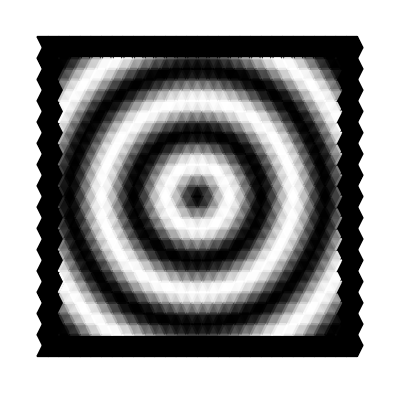

```mathematica
{FinalValuedVertices,FinalValuedEdges,FinalValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero,GRAPHIQUE} = ComputeValuedPseudoManifold[sx,sy];
```

```mathematica
{EdgesGrapheDual,ListeCoordonneesNoeudsGrapheDual} = ComputeDualGraph[FinalValuedVertices,FinalValuedEdges,FinalValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero];
```

NbCCsGmin = 86

NUMEROSFACESMINIMALES = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,74,76,89,90,91,92,109,110,119,120,121,122,141,142,149,150,151,152,173,179,180,181,182,187,209,210,211,212,235,239,240,241,242,254,256,269,270,271,272,275,282,283,299,300,301,302,320,327,329,330,331,332,334,359,360,361,362,364,370,389,390,391,392,394,400,419,420,421,422,424,430,436,442,448,449,450,451,452,454,460,479,480,481,482,484,490,509,510,511,512,514,539,540,541,542,560,569,570,571,572,582,597,599,600,601,602,605,613,614,616,629,630,631,632,659,660,661,662,685,689,690,691,692,697,719,720,721,722,742,743,749,750,751,752,770,771,779,780,781,782,794,796,799,809,810,811,812,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,975,977,989,990,991,992,1001,1002,1019,1020,1021,1022,1029,1030,1049,1050,1051,1052,1058,1079,1080,1081,1082,1104,1109,1110,1111,1112,1116,1139,1140,1141,1142,1155,1157,1169,1170,1171,1172,1188,1189,1196,1199,1200,1201,1202,1204,1211,1229,1230,1231,1232,1257,1259,1260,1261,1262,1281,1287,1289,1290,1291,1292,1311,1317,1319,1320,1321,1322,1323,1329,1335,1341,1347,1349,1350,1351,1352,1371,1377,1379,1380,1381,1382,1401,1407,1409,1410,1411,1412,1437,1439,1440,1441,1442,1451,1469,1470,1471,1472,1474,1489,1499,1500,1501,1502,1515,1517,1518,1526,1529,1530,1531,1532,1559,1560,1561,1562,1566,1589,1590,1591,1592,1614,1619,1620,1621,1622,1628,1629,1649,1650,1651,1652,1660,1661,1679,1680,1681,1682,1692,1695,1697,1709,1710,1711,1712,1739,1740,1741,1742,1743,1744,1745,1746,1747,1748,1749,1750,1751,1752,1753,1754,1755,1756,1757,1758,1759,1760,1761,1762,1763,1764,1765,1766,1767,1768,1769,1770,1771,1772,1773,1774,1775,1776,1777,1778,1779,1780,1781,1782,1783,1784,1785,1786,1787,1788,1789,1790,1791,1792,1793,1794,1795,1796,1797,1798,1799,1800}

INIT -- GraphePassé = {0<->1,0<->2,0<->3,0<->4,0<->5,0<->6,0<->7,0<->8,0<->9,0<->10,0<->11,0<->12,0<->13,0<->14,0<->15,0<->16,0<->17,0<->18,0<->19,0<->20,0<->21,0<->22,0<->23,0<->24,0<->25,0<->26,0<->27,0<->28,0<->29,0<->30,0<->31,0<->32,0<->33,0<->34,0<->35,0<->36,0<->37,0<->38,0<->39,0<->40,0<->41,0<->42,0<->43,0<->44,0<->45,0<->46,0<->47,0<->48,0<->49,0<->50,0<->51,0<->52,0<->53,0<->54,0<->55,0<->56,0<->57,0<->58,0<->59,0<->60,0<->61,0<->62,0<->74,0<->76,0<->89,0<->90,0<->91,0<->92,0<->109,0<->110,0<->119,0<->120,0<->121,0<->122,0<->141,0<->142,0<->149,0<->150,0<->151,0<->152,0<->173,0<->179,0<->180,0<->181,0<->182,0<->187,0<->209,0<->210,0<->211,0<->212,0<->235,0<->239,0<->240,0<->241,0<->242,0<->254,0<->256,0<->269,0<->270,0<->271,0<->272,0<->275,0<->282,0<->283,0<->299,0<->300,0<->301,0<->302,0<->320,0<->327,0<->329,0<->330,0<->331,0<->332,0<->334,0<->359,0<->360,0<->361,0<->362,0<->364,0<->370,0<->389,0<->390,0<->391,0<->392,0<->394,0<->400,0<->419,0<->420,0<->421,0<->422,0<->424,0<->430,0<->436,0<->442,0<->448,0<->449,0<->450,0<->451,0<->452,0<->454,0<->460,0<->479,0<->480,0<->481,0<->482,0<->484,0<->490,0<->509,0<->510,0<->511,0<->512,0<->514,0<->539,0<->540,0<->541,0<->542,0<->560,0<->569,0<->570,0<->571,0<->572,0<->582,0<->597,0<->599,0<->600,0<->601,0<->602,0<->605,0<->613,0<->614,0<->616,0<->629,0<->630,0<->631,0<->632,0<->659,0<->660,0<->661,0<->662,0<->685,0<->689,0<->690,0<->691,0<->692,0<->697,0<->719,0<->720,0<->721,0<->722,0<->742,0<->743,0<->749,0<->750,0<->751,0<->752,0<->770,0<->771,0<->779,0<->780,0<->781,0<->782,0<->794,0<->796,0<->799,0<->809,0<->810,0<->811,0<->812,0<->839,0<->840,0<->841,0<->842,0<->843,0<->844,0<->845,0<->846,0<->847,0<->848,0<->849,0<->850,0<->851,0<->852,0<->853,0<->854,0<->855,0<->856,0<->857,0<->858,0<->859,0<->860,0<->861,0<->862,0<->863,0<->864,0<->865,0<->866,0<->867,0<->868,0<->869,0<->870,0<->871,0<->872,0<->873,0<->874,0<->875,0<->876,0<->877,0<->878,0<->879,0<->880,0<->881,0<->882,0<->883,0<->884,0<->885,0<->886,0<->887,0<->888,0<->889,0<->890,0<->891,0<->892,0<->893,0<->894,0<->895,0<->896,0<->897,0<->898,0<->899,0<->900,0<->901,0<->902,0<->903,0<->904,0<->905,0<->906,0<->907,0<->908,0<->909,0<->910,0<->911,0<->912,0<->913,0<->914,0<->915,0<->916,0<->917,0<->918,0<->919,0<->920,0<->921,0<->922,0<->923,0<->924,0<->925,0<->926,0<->927,0<->928,0<->929,0<->930,0<->931,0<->932,0<->933,0<->934,0<->935,0<->936,0<->937,0<->938,0<->939,0<->940,0<->941,0<->942,0<->943,0<->944,0<->945,0<->946,0<->947,0<->948,0<->949,0<->950,0<->951,0<->952,0<->953,0<->954,0<->955,0<->956,0<->957,0<->958,0<->959,0<->960,0<->961,0<->962,0<->975,0<->977,0<->989,0<->990,0<->991,0<->992,0<->1001,0<->1002,0<->1019,0<->1020,0<->1021,0<->1022,0<->1029,0<->1030,0<->1049,0<->1050,0<->1051,0<->1052,0<->1058,0<->1079,0<->1080,0<->1081,0<->1082,0<->1104,0<->1109,0<->1110,0<->1111,0<->1112,0<->1116,0<->1139,0<->1140,0<->1141,0<->1142,0<->1155,0<->1157,0<->1169,0<->1170,0<->1171,0<->1172,0<->1188,0<->1189,0<->1196,0<->1199,0<->1200,0<->1201,0<->1202,0<->1204,0<->1211,0<->1229,0<->1230,0<->1231,0<->1232,0<->1257,0<->1259,0<->1260,0<->1261,0<->1262,0<->1281,0<->1287,0<->1289,0<->1290,0<->1291,0<->1292,0<->1311,0<->1317,0<->1319,0<->1320,0<->1321,0<->1322,0<->1323,0<->1329,0<->1335,0<->1341,0<->1347,0<->1349,0<->1350,0<->1351,0<->1352,0<->1371,0<->1377,0<->1379,0<->1380,0<->1381,0<->1382,0<->1401,0<->1407,0<->1409,0<->1410,0<->1411,0<->1412,0<->1437,0<->1439,0<->1440,0<->1441,0<->1442,0<->1451,0<->1469,0<->1470,0<->1471,0<->1472,0<->1474,0<->1489,0<->1499,0<->1500,0<->1501,0<->1502,0<->1515,0<->1517,0<->1518,0<->1526,0<->1529,0<->1530,0<->1531,0<->1532,0<->1559,0<->1560,0<->1561,0<->1562,0<->1566,0<->1589,0<->1590,0<->1591,0<->1592,0<->1614,0<->1619,0<->1620,0<->1621,0<->1622,0<->1628,0<->1629,0<->1649,0<->1650,0<->1651,0<->1652,0<->1660,0<->1661,0<->1679,0<->1680,0<->1681,0<->1682,0<->1692,0<->1695,0<->1697,0<->1709,0<->1710,0<->1711,0<->1712,0<->1739,0<->1740,0<->1741,0<->1742,0<->1743,0<->1744,0<->1745,0<->1746,0<->1747,0<->1748,0<->1749,0<->1750,0<->1751,0<->1752,0<->1753,0<->1754,0<->1755,0<->1756,0<->1757,0<->1758,0<->1759,0<->1760,0<->1761,0<->1762,0<->1763,0<->1764,0<->1765,0<->1766,0<->1767,0<->1768,0<->1769,0<->1770,0<->1771,0<->1772,0<->1773,0<->1774,0<->1775,0<->1776,0<->1777,0<->1778,0<->1779,0<->1780,0<->1781,0<->1782,0<->1783,0<->1784,0<->1785,0<->1786,0<->1787,0<->1788,0<->1789,0<->1790,0<->1791,0<->1792,0<->1793,0<->1794,0<->1795,0<->1796,0<->1797,0<->1798,0<->1799,0<->1800}

noeudsdejavus = {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,74,76,89,90,91,92,109,110,119,120,121,122,141,142,149,150,151,152,173,179,180,181,182,187,209,210,211,212,235,239,240,241,242,254,256,269,270,271,272,275,282,283,299,300,301,302,320,327,329,330,331,332,334,359,360,361,362,364,370,389,390,391,392,394,400,419,420,421,422,424,430,436,442,448,449,450,451,452,454,460,479,480,481,482,484,490,509,510,511,512,514,539,540,541,542,560,569,570,571,572,582,597,599,600,601,602,605,613,614,616,629,630,631,632,659,660,661,662,685,689,690,691,692,697,719,720,721,722,742,743,749,750,751,752,770,771,779,780,781,782,794,796,799,809,810,811,812,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,896,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,975,977,989,990,991,992,1001,1002,1019,1020,1021,1022,1029,1030,1049,1050,1051,1052,1058,1079,1080,1081,1082,1104,1109,1110,1111,1112,1116,1139,1140,1141,1142,1155,1157,1169,1170,1171,1172,1188,1189,1196,1199,1200,1201,1202,1204,1211,1229,1230,1231,1232,1257,1259,1260,1261,1262,1281,1287,1289,1290,1291,1292,1311,1317,1319,1320,1321,1322,1323,1329,1335,1341,1347,1349,1350,1351,1352,1371,1377,1379,1380,1381,1382,1401,1407,1409,1410,1411,1412,1437,1439,1440,1441,1442,1451,1469,1470,1471,1472,1474,1489,1499,1500,1501,1502,1515,1517,1518,1526,1529,1530,1531,1532,1559,1560,1561,1562,1566,1589,1590,1591,1592,1614,1619,1620,1621,1622,1628,1629,1649,1650,1651,1652,1660,1661,1679,1680,1681,1682,1692,1695,1697,1709,1710,1711,1712,1739,1740,1741,1742,1743,1744,1745,1746,1747,1748,1749,1750,1751,1752,1753,1754,1755,1756,1757,1758,1759,1760,1761,1762,1763,1764,1765,1766,1767,1768,1769,1770,1771,1772,1773,1774,1775,1776,1777,1778,1779,1780,1781,1782,1783,1784,1785,1786,1787,1788,1789,1790,1791,1792,1793,1794,1795,1796,1797,1798,1799,1800}

Q[14] = {1526<->626,605<->1505,275<->1145,1196<->266}

Q[19] = {685<->1555,1566<->636,235<->1135,1116<->216}

Q[35] = {843<->1713,1768<->838}

Q[66] = {1401<->531,490<->1420,1281<->381,370<->1270}

Q[93] = {1437<->567,514<->1444,1257<->357,334<->1234}

Q[94] = {560<->1460,1451<->551,1211<->341,320<->1250}

Q[172] = {743<->1613,1628<->698,173<->1073,1058<->158}

Q[203] = {799<->1698,1697<->798,794<->1693,1692<->793,109<->1008,1002<->103,977<->78,74<->973}

Q[228] = {839<->1738,1712<->813,89<->988,933<->63,962<->63,58<->988}

Q[278] = {1614<->714,697<->1597,187<->1057,1104<->174}

Q[297] = {1377<->478,454<->1353,1317<->418,394<->1293}

Q[348] = {1517<->617,614<->1514,1157<->287,254<->1184}

Q[397] = {597<->1467,1474<->544,327<->1227,1204<->304}

Q[484] = {771<->1671,1660<->760,141<->1011,1030<->100}

Q[586] = {1371<->472,460<->1359,1311<->412,400<->1299}

Q[645] = {1489<->589,582<->1482,1189<->319,282<->1212}

Q[694] = {742<->1642,1629<->729,1407<->537,484<->1414,1287<->387,364<->1264,1029<->159,142<->1072}

Q[714] = {770<->1669,1661<->762,110<->1009,1001<->102}

Q[739] = {1661<->791,770<->1700,110<->1010,1001<->101}

Q[750] = {1517<->618,614<->1513,1157<->258,254<->1153}

Q[759] = {597<->1496,1474<->575,327<->1226,1204<->305}

Q[784] = {1489<->619,582<->1512,1189<->289,282<->1182}

Q[808] = {1371<->501,460<->1390,1311<->411,400<->1300}

Q[828] = {1437<->537,514<->1414,1257<->387,334<->1264}

Q[840] = {743<->1642,1628<->729,173<->1072,1058<->159}

Q[882] = {799<->1669,1692<->762,109<->1009,1002<->102}

Q[886] = {1629<->759,742<->1672,142<->1042,1029<->129}

Q[892] = {1697<->797,794<->1694,977<->107,74<->1004}

Q[934] = {1518<->619,613<->1512,1188<->289,283<->1182}

Q[963] = {1518<->618,613<->1513,283<->1153,1188<->258}

Q[975] = {697<->1567,1614<->684,1104<->204,187<->1087}

Q[1100] = {771<->1641,1660<->730,141<->1041,1030<->130}

Q[1119] = {771<->1670,1660<->761,141<->1040,1030<->131}

Q[1137] = {616<->1516,1515<->615,1401<->501,490<->1390,1281<->411,370<->1300,1155<->285,256<->1186}

Q[1165] = {1407<->508,484<->1383,1287<->388,364<->1263}

Q[1180] = {613<->1483,1518<->588,1188<->288,283<->1183}

Q[1194] = {1451<->581,560<->1490,320<->1220,1211<->311}

Q[1219] = {770<->1670,1661<->761,1001<->131,110<->1040}

Q[1226] = {742<->1641,1629<->730,142<->1041,1029<->130}

Q[1240] = {796<->1696,1695<->795,975<->105,76<->1006}

Q[1257] = {1377<->507,454<->1384,1317<->417,394<->1294}

Q[1434] = {1695<->825,796<->1726,76<->976,945<->75,975<->75,46<->976}

Q[1449] = {605<->1475,1526<->596,1196<->296,275<->1175}

Q[1515] = {867<->1737,1744<->814}

Q[1524] = {1515<->645,616<->1546,256<->1156,1155<->255}

Q[1546] = {685<->1584,1566<->667,235<->1134,1116<->217}

Q[1570] = {1407<->507,484<->1384,1287<->417,364<->1294}

Q[1581] = {1341<->471,1341<->441,430<->1330,430<->1360}

Q[1596] = {799<->1699,1692<->792,685<->1585,1566<->666,235<->1105,1116<->186,109<->979,1002<->72}

Q[1662] = {1697<->827,794<->1724,977<->77,74<->974}

Q[1663] = {1347<->477,1347<->447,424<->1324,424<->1354}

Q[1693] = {560<->1459,1451<->552,320<->1219,1211<->312}

Q[1735] = {947<->77,44<->974}

Q[1793] = {1489<->590,582<->1481,1189<->290,282<->1181}

Q[1803] = {1323<->453,448<->1348,448<->1378,1323<->423}

Q[1807] = {1377<->477,454<->1354,1317<->447,394<->1324}

Q[1851] = {1517<->647,614<->1544,1157<->257,254<->1154}

Q[1855] = {1371<->471,460<->1360,1311<->441,400<->1330}

Q[1864] = {1329<->459,442<->1342,442<->1372,1329<->429}

Q[1894] = {1526<->627,605<->1504,1196<->297,275<->1174}

Q[1914] = {743<->1643,1628<->728,173<->1043,1058<->128}

Q[1953] = {1614<->715,697<->1596,1104<->205,187<->1086}

Q[2174] = {1401<->502,490<->1389,1281<->382,370<->1269}

Q[2313] = {597<->1497,1474<->574,327<->1197,1204<->274}

Q[2406] = {479<->1378,1352<->453,449<->1348,1322<->423}

Q[2507] = {1437<->538,514<->1413,1257<->358,334<->1233}

Q[2967] = {509<->1408,1382<->483,419<->1318,1292<->393}

Q[2969] = {1335<->465,436<->1336,436<->1366,1335<->435}

Q[3164] = {943<->73,48<->978}

Q[4052] = {809<->1708,1682<->783,119<->1018,992<->93}

Q[4216] = {539<->1438,1412<->513,389<->1288,1262<->363}

Q[4438] = {949<->79,42<->972}

Q[5039] = {855<->1725,1756<->826}

Q[5994] = {857<->1727,1754<->824}

Q[6194] = {957<->87,34<->964}

Q[6332] = {569<->1468,1442<->543,359<->1258,1232<->333}

Q[6987] = {853<->1723,1758<->828}

Q[8360] = {941<->71,50<->980}

Q[8886] = {845<->1715,1766<->836}

Q[9396] = {599<->1498,1472<->573,329<->1228,1202<->303}

Q[10075] = {859<->1729,1752<->822}

Q[10494] = {779<->1678,1652<->753,149<->1048,1022<->123}

Q[10706] = {935<->65,56<->986}

Q[10944] = {951<->81,40<->970}

Q[12112] = {851<->1721,1760<->830}

Q[13089] = {865<->1735,1746<->816}

Q[13182] = {629<->1528,1502<->603,299<->1198,1172<->273}

Q[16428] = {749<->1648,1622<->723,179<->1078,1052<->153,939<->69,52<->982}

Q[16545] = {861<->1731,1750<->820}

Q[16975] = {659<->1558,1532<->633,269<->1168,1142<->243}

Q[18090] = {955<->85,36<->966}

Q[18447] = {849<->1719,1762<->832}

Q[18620] = {953<->83,38<->968}

Q[18949] = {847<->1717,1764<->834}

Q[19575] = {689<->1588,1562<->663,239<->1138,1112<->213}

Q[19647] = {719<->1618,1592<->693,209<->1108,1082<->183}

Q[19758] = {937<->67,54<->984}

Q[19953] = {863<->1733,1748<->818}

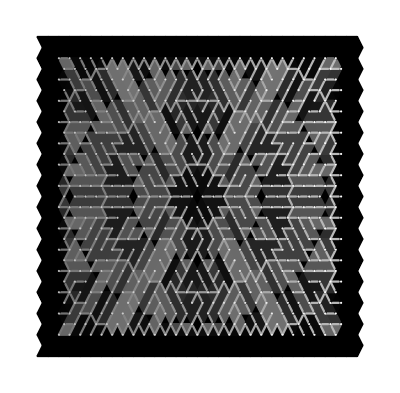

```mathematica
{FinalValuedVerticesLAURENT,FinalValuedEdgesLAURENT,FinalValuedFacesLAURENT,ParentsDirectsParNumero,EnfantsDirectsParNumero} = ComputeSimplicialStackUSINGFUNCTIONversion4[FinalValuedVertices,FinalValuedEdges,FinalValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero];
```

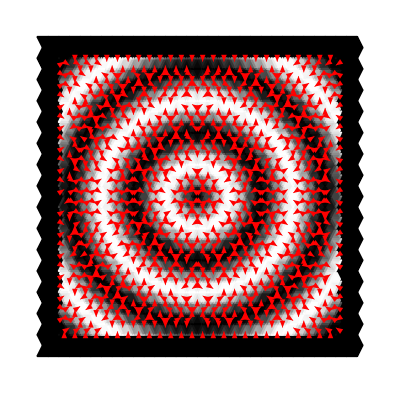

```mathematica
ChampsDeGradient = ComputeGradient[FinalValuedVerticesLAURENT,FinalValuedEdgesLAURENT,FinalValuedFacesLAURENT,ParentsDirectsParNumero,EnfantsDirectsParNumero];
```

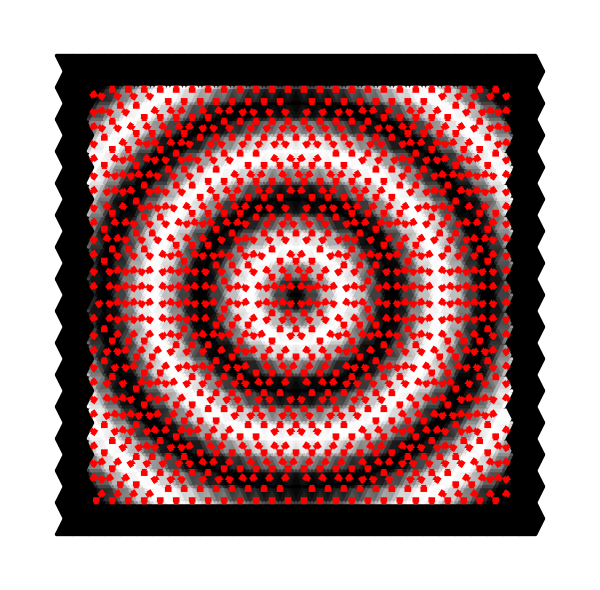
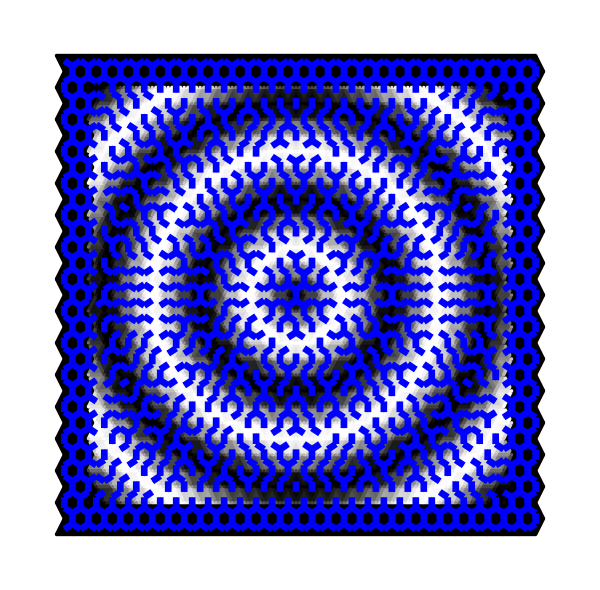

```mathematica
GraphDualParGradient = ComputeDualGraphFromGradientVectorField[FinalValuedVerticesLAURENT,FinalValuedEdgesLAURENT,FinalValuedFacesLAURENT,ParentsDirectsParNumero,EnfantsDirectsParNumero,ChampsDeGradient];
Print[GraphDualParGradient];
```

# Partie Calcul MSF (Prim) & Comparaison

## Calcul MSF algo Laurent

```mathematica
ComputeMSFGrapheDual[FinalValuedVertices_,FinalValuedEdges_,FinalValuedFaces_,ParentsDirectsParNumero_,EnfantsDirectsParNumero_]:=Block[{NbFaces,NbEdges,NumeroVertexARTIFICIEL,EdgesGrapheDualARTIFICIELS,WeightsEdgesGrapheDualARTIFICIELS,ListeCoordonneesNoeudsGrapheDual,EdgesGrapheDual,WeightsEdgesGraphDual,numeroedge,NumerosParentsEdge,ValeurFace1Parente,ValeurFace2Parente,ValeurEdge,NumeroFace1Parente,barycentreparent1,NumeroFace2Parente,barycentreparent2,g,MinimumSpanningTreeARTIFICIEL,MSFWithMinima,listeparentsedge,GrapheDualParMSF,cpt,graphedualinitialplot,data,facesGmin,edgesGmin},

NbFaces = Dimensions[FinalValuedFaces][[1]];
NbEdges = Dimensions[FinalValuedEdges][[1]];

data =ComputeNumerosMinimalDeuxFacesAUSENSGRAPHEDUALversion2[FinalValuedVertices,FinalValuedEdges,FinalValuedFaces,ParentsDirectsParNumero,EnfantsDirectsParNumero];
facesGmin = data[[4]];
edgesGmin = data[[5]];

NumeroVertexARTIFICIEL = 0;
(* on raccroche le point à l'infini artificiel aux minima et on pndère ces edges par "-1" *)
EdgesGrapheDualARTIFICIELS = Table[NumeroVertexARTIFICIEL<-> facesGmin[[numeronoeud]],{numeronoeud, 1, Dimensions[facesGmin][[1]]}];
WeightsEdgesGrapheDualARTIFICIELS = Table[-1,{numeronoeud, 1, Dimensions[facesGmin][[1]]}];

ListeCoordonneesNoeudsGrapheDual = {NumeroVertexARTIFICIEL->({-5,-5}//N)}~Join~data[[7]];

(* on ajoute EN MEME TEMPS les edges et leurs poids pour être sur que dans le bon ordre *)
EdgesGrapheDual = {};
WeightsEdgesGraphDual = {};
For[numeroedge = NbFaces+1,numeroedge≤ NbFaces+NbEdges,numeroedge++,{
NumerosParentsEdge = ComputeParentsDirects[ParentsDirectsParNumero,numeroedge];
(* si deux parents, il existe un edge dual *)
If[Dimensions[NumerosParentsEdge][[1]]==2,{
EdgesGrapheDual = Append[EdgesGrapheDual,NumerosParentsEdge[[1]] <-> NumerosParentsEdge[[2]]];
ValeurEdge = FinalValuedEdges[[numeroedge-NbFaces]][[2]];
WeightsEdgesGraphDual = Append[WeightsEdgesGraphDual,ValeurEdge]; 
}];
}];

g = Graph[{NumeroVertexARTIFICIEL},EdgesGrapheDual~Join~EdgesGrapheDualARTIFICIELS,EdgeWeight->WeightsEdgesGraphDual~Join~WeightsEdgesGrapheDualARTIFICIELS,VertexCoordinates->ListeCoordonneesNoeudsGrapheDual];
MinimumSpanningTreeARTIFICIEL = FindSpanningTree[g,Method->"Prim"];
MSFWithMinima = VertexDelete[MinimumSpanningTreeARTIFICIEL,NumeroVertexARTIFICIEL];

graphedualinitialplot = Graph[EdgesGrapheDual,VertexCoordinates->ListeCoordonneesNoeudsGrapheDual];
GrapheDualParMSF = HighlightGraph[graphedualinitialplot,MSFWithMinima,GraphHighlightStyle->"Thick",ImageSize->600];

(* on rajoute les edges des minima qui n'étaient pas isolés (cad composantes connexes car foret relative avec cycles) *)
For[cpt=1,cpt≤Dimensions[edgesGmin][[1]],cpt++,{
MSFWithMinima = EdgeAdd[MSFWithMinima,edgesGmin[[cpt]]];
}];

Print["graphedualinitialplot =",graphedualinitialplot];

{EdgeList[MSFWithMinima],ListeCoordonneesNoeudsGrapheDual,HighlightGraph[graphedualinitialplot,MSFWithMinima,GraphHighlightStyle->"Thick",ImageSize->600],graphedualinitialplot,GrapheDualParMSF,MSFWithMinima}
];
```

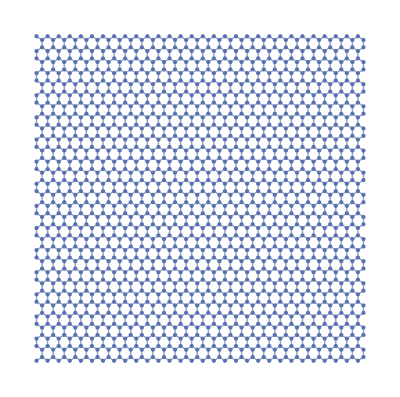
graphedualinitialplot =-Graphics-

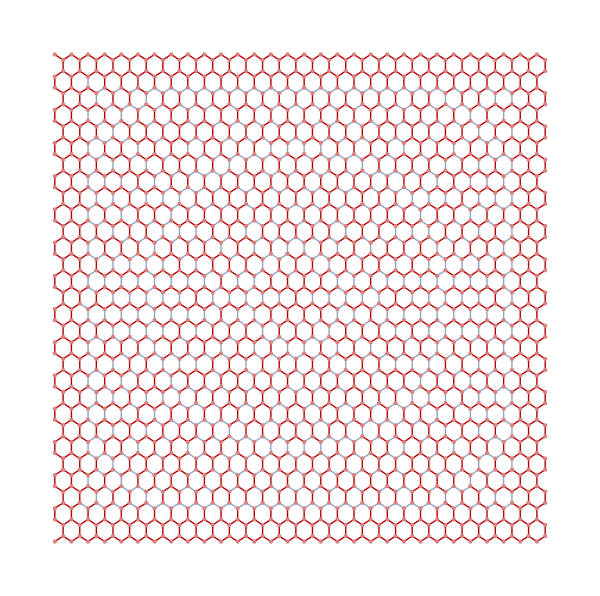

```mathematica
MSF = ComputeMSFGrapheDual[FinalValuedVerticesLAURENT,FinalValuedEdgesLAURENT,FinalValuedFacesLAURENT,ParentsDirectsParNumero,EnfantsDirectsParNumero];
Print[MSF[[3]]];
```

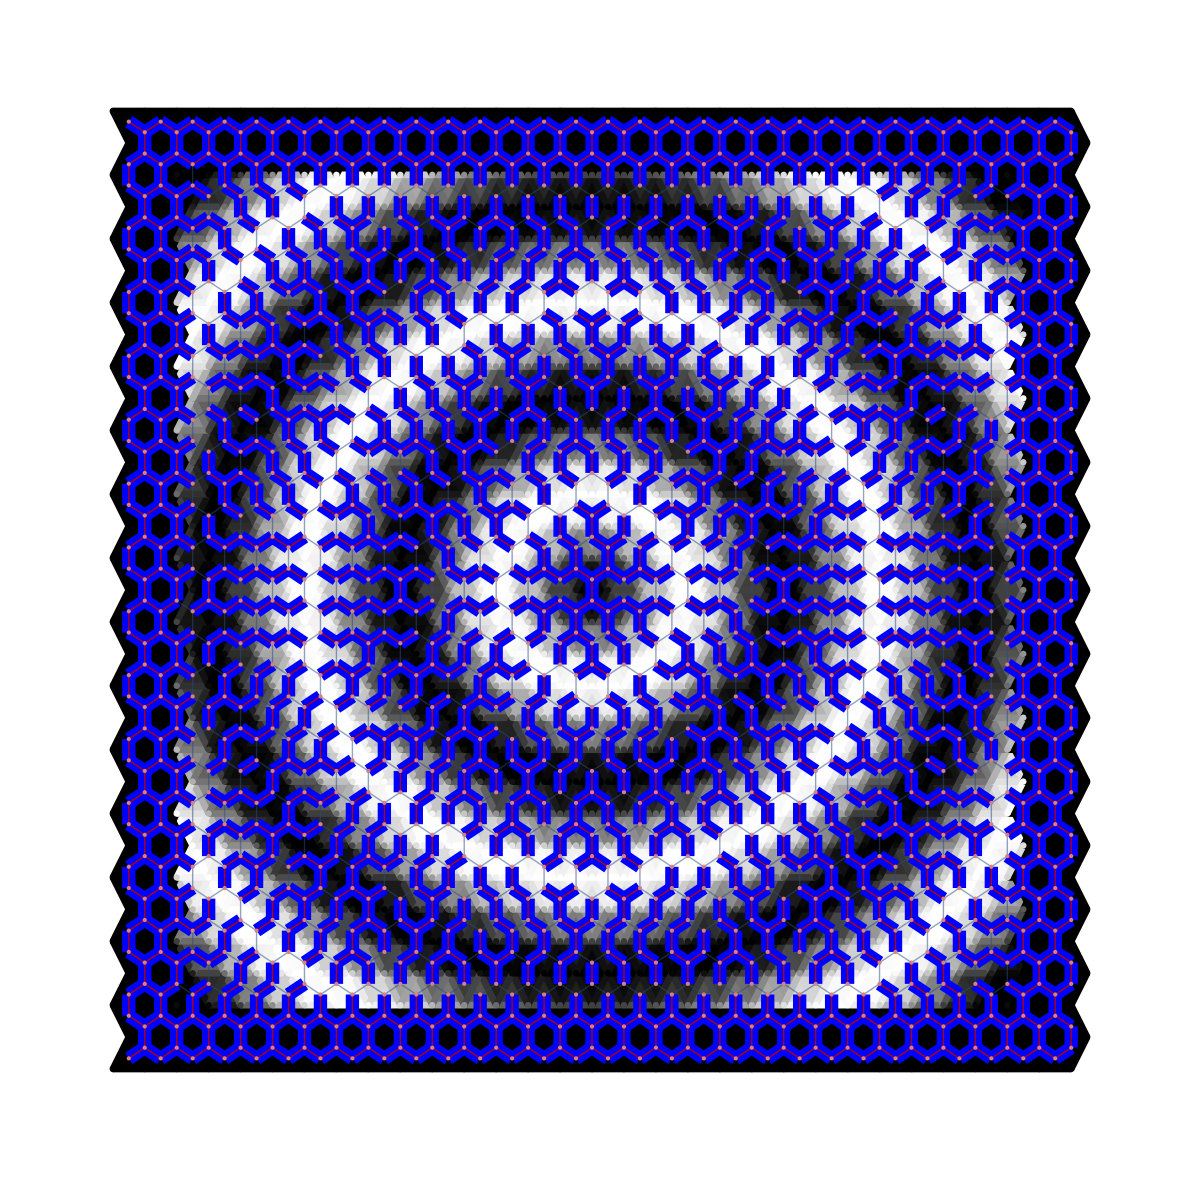
-Graphics--Graphics--Graphics-

```mathematica
Print[GraphDualParGradient[[2]],MSF[[3]],Show[GraphDualParGradient[[2]],MSF[[3]],ImageSize-> 1200]]
```

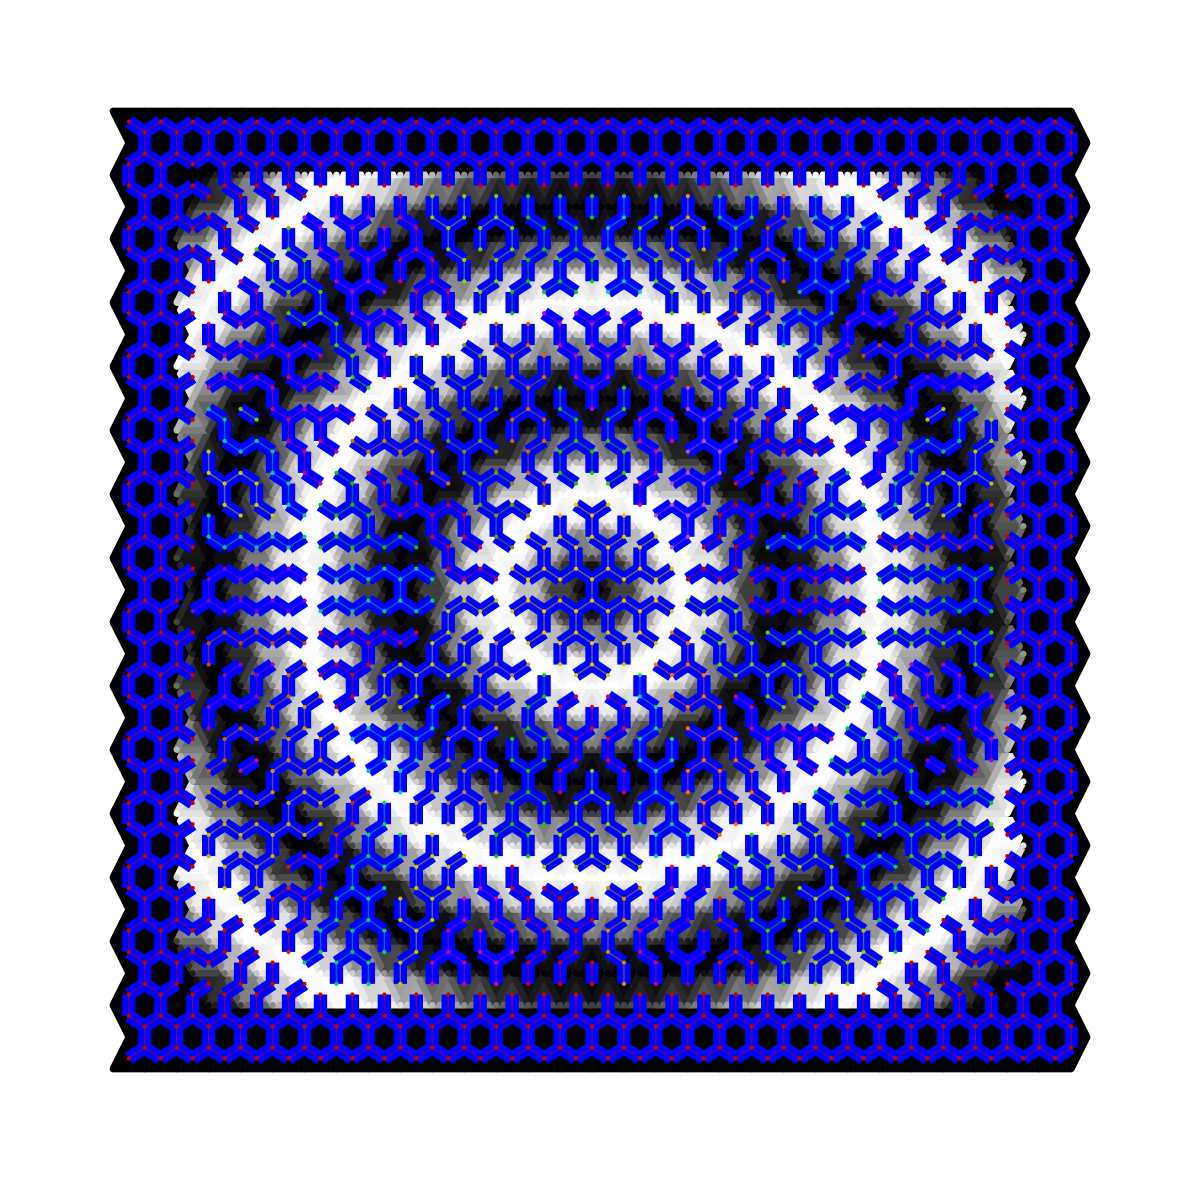

```mathematica
Show[GraphDualParGradient[[2]],HighlightGraph[MSF[[6]],ConnectedGraphComponents[MSF[[6]]]],ImageSize->1200]
```